### Parameters

With zh=1

```mathematica
ω1ot=-5.16952097576222954940461885889722499194572185535488411636773071714438971882811`55.-4.76357011692046086364514648370905218950138549522150190381951475957642922361821`55. ⅈ;
```

```mathematica
ωfund=3.11945159116590140667726984186100634853095499472948675543437548096051622380119`55.-2.74667574434060639673424074409714552362302736020758738193589764462283480845456`55. ⅈ;
```

### A=0.15

```mathematica
FileName="BB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d15";
FolderName="home/giulio/University/PhD/Simulations/";
TypeOfFile="bulk";
init=0;
end=3000;
each=5;
FNames=Table[StringJoin[TypeOfFile<>"_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
Name1=Table[StringJoin["/"<>FolderName<>FileName<>"/",
FNames[[i]],".h5"],{i,FNames//Length}];
dt=Import[Name1[[-1]],"Attributes"][[3,1]];
Timing[Obj=Module[{lastValid},Table[If[FileExistsQ[Name1[[i]]],lastValid=Import[Name1[[i]],"Data"];
lastValid,lastValid (*reuse previous if missing*)],{i,1,Length[Name1]}]];
(*Obj=Table[Import[Name1[[i]],"Data"](*[[1]]*),{i,1,Name1//Length}]*)];//AbsoluteTiming
Print["you have imported: "<>ToString[FNames//Length]<>" snapshot"];
(*"/home/giulio/University/PhD/JeccoGt2/examples/BB_QNM_1D_4p1_Vchannel_xpert/"*)
Print["defining times vector ..."]
times=Table[tim dt each+init dt,{tim,1,Obj//Length}];
(*snapshots=Table[(tim-1)  each+init ,{tim,1,Obj//Length}];*)
nt=times//Length;
Print["dt = "<>ToString[dt]]
Print["final time = "<>ToString[Import[Name1[[-1]],"Attributes"][[3,2]]//FullForm]]
```

{19.0493,Null}

you have imported: 601 snapshot

defining times vector ...

dt = 0.00363636

final time = 10.909090909091276`

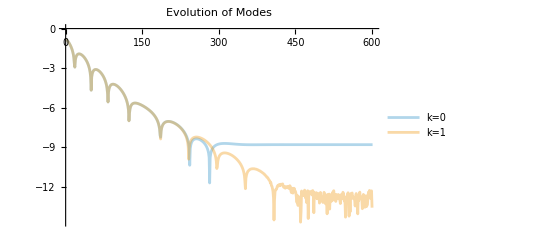

```mathematica
(*Parameters-Adjust these to match your simulation setup*)
g3=Obj[[;;,4,1,1,-1]];
(*4. Visualization*)
(*Plot the real part (oscillations) and the Magnitude (decay)*)
ListLinePlot[{(Re[g3])//Abs//Log[10,#]&,(Re[g3])-Re[g3[[-1]]]//Abs//Log[10,#]&},PlotRange->All,FrameLabel->{"Time Index","Amplitude"},PlotLabel->"Evolution of Modes",ImageSize->Full,PlotLegends->Placed[{"k=0","k=1","k=2","k=3","k=4","k=5"},{Right,Top}],PlotStyle->{Opacity[0.4]}]
```

```mathematica
aaa=22;
bbb=103;
Timess=times;(*Table[(*dt*)dt (each i),{i,0,g3[[;;,1,1]]//Length}];*)
Lastg3=g3[[-1]];
Datag3=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*-Lastg3*)(*Lastg3[[1,1]]*))(*//Abs//Log*)}];
Datag3Log=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*Lastg3*))//Abs//Log}];
```

```mathematica
A0d15FitResgWr=NonlinearModelFit[Datag3,(*-wi (t-t0)+A1*)(*0.05 E^(-wi (t-t0))Cos[wr (t-t0)+ϕ]*)0.15 E^(-wi1(t-t01))Cos[wr1(t-t01)+ϕ1]/.wi1->Im[-ω1ot]/.wr1->Re[ω1ot](*/.A0d15FitResgWr2["BestFitParameters"]*)(*+A2 Exp[-wi2(t-t01)]Cos[wr2(t-t01)+ϕ2]*)(*+A2 +wi2(t-t01)*)(*+ 0.1 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w1i (t-t0))Cos[w1r (t-t0)+ϕ1]+*)(*A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0]*) (*A0oft[t]*)(*+a1g  E^(-w1gi (t))Cos[w1gr (t-t0)+ϕ1g]*)(*+a2g E^(-w2gi (t-t0))Cos[ w2gr (t-t0)+ϕ2g] *)
,{{A1,0.15},ϕ1,{wi1,5.3},{wr1,4.8},{t01,20}(*,{A2},ϕ2,{wi2},{wr2},t02*)},{t(*,Timess[[aaa]],Timess[[bbb]]*)},MaxIterations->5000,ConfidenceLevel->0.9999999999];
```

```mathematica
A0d15FitResgWr["BestFitParameters"]
A0d15FitResgWr2["BestFitParameters"]
```

{A1→0.15,ϕ1→106.822,wi1→5.3,wr1→4.8,t01→0.00966174}

A0d15FitResgWr2[BestFitParameters]

```mathematica
ω
```

ω

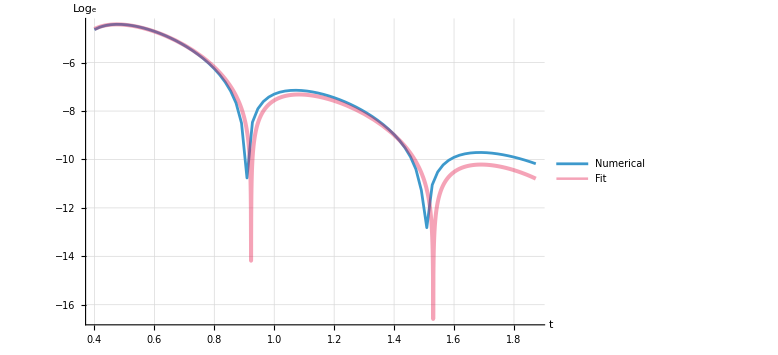

```mathematica
Show[ListPlot[Datag3Log,PlotStyle->PointSize[0.01],PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large,Joined->True],Plot[A0d15FitResgWr[t]//Abs//Log,{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.4],RGBColor[0.9,.1,0.3]}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

```mathematica
2
```

2

```mathematica
nt
```

601

```mathematica
ClearAll[t];
aaa=240;
bbb=363;
Timess=times;(*Table[(*dt*)dt (each i),{i,0,g3[[;;,1,1]]//Length}];*)
Datag3=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*-Lastg3*)(*Lastg3[[1,1]]*))(*//Abs//Log*)}];
Datag3Log=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*Lastg3*))//Abs//Log}];
A0d15FitResgWr2=NonlinearModelFit[Datag3,(*-wi (t-t0)+A1*)A2 E^(-wi2 (t-t01))Cos[wr2 (t-t01)+ϕ2]/.wi2->Im[-ωfund]/.wr2->Re[ωfund]/.A0d15FitResgWr["BestFitParameters"](*//Abs//Log*)(*+ 0.1 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w1i (t-t0))Cos[w1r (t-t0)+ϕ1]+*)(*A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0]*) (*A0oft[t]*)(*+a1g  E^(-w1gi (t))Cos[w1gr (t-t0)+ϕ1g]*)(*+a2g E^(-w2gi (t-t0))Cos[ w2gr (t-t0)+ϕ2g] *)
,{(*a1g,a2g,A2,A0,ϕ1g,ϕ2g,w1gi,w1gr,w2gi,w2gr,ϕ2,ϕ0,*)A2,ϕ2,t01,wi2,wr2},{t(*,Timess[[aaa]],Timess[[bbb]]*)},MaxIterations->5000,ConfidenceLevel->0.9999999999];
```

```mathematica
A0d15FitResgWr2["BestFitParameters"]
A0d15FitResgWr["BestFitParameters"]
```

{A2→-0.00277611,ϕ2→0.492435,t01→1.,wi2→1.,wr2→1.}

{A1→0.15,ϕ1→106.822,wi1→5.3,wr1→4.8,t01→0.00966174}

```mathematica
0.15^3
```

0.003375

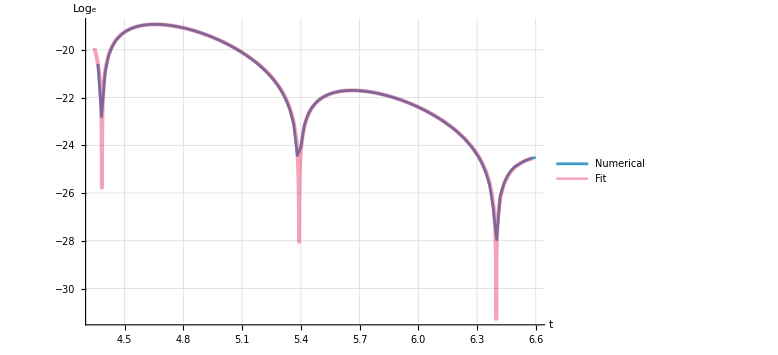

```mathematica
Timess=Table[(*dt*)dt (each i),{i,0,Obj//Length}];
Show[ListPlot[Datag3Log,PlotStyle->PointSize[0.01],PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large,Joined->True],Plot[A0d15FitResgWr2[t]//Abs//Log,{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.4],RGBColor[0.9,.1,0.3]}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

```mathematica
2
```

2

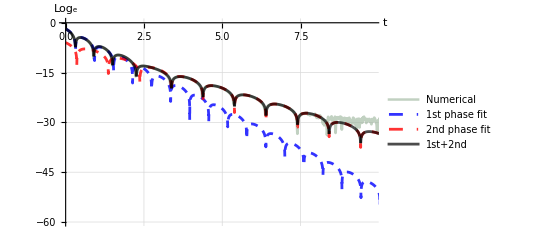

```mathematica
Show[ListPlot[Transpose[{Timess[[;;-2]],(g3[[;;]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*Lastg3*))//Abs//Log}],PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.6],RGBColor[0.6,0.7,0.6]},PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Full,Joined->True],Plot[A0d15FitResgWr[t]//Abs//Log,{t,Timess[[1]],Timess[[-1]]},PlotLegends->{"1st phase fit"},PlotStyle->{Blue,Opacity[0.8],Dashed},PlotLegends->Placed["Numerical", {Center}]],Plot[A0d15FitResgWr2[t]//Abs//Log,{t,Timess[[1]],Timess[[-1]]},PlotLegends->{"2nd phase fit"},PlotStyle->{Red,Opacity[0.8],Dashed}],Plot[A0d15FitResgWr[t]+A0d15FitResgWr2[t]//Abs//Log,{t,Timess[[1]],Timess[[-1]]},PlotLegends->{"1st+2nd"},PlotStyle->{Black,Opacity[0.7],Point}],PlotRange->{{0,9.8},{-60,0.1}},AxesLabel->{"t","Log_e"}]
```

```mathematica
Export["/home/giulio/Pictures/Jecco_QNM_gxy"<>FileName<>".pdf",%]
```

/home/giulio/Pictures/Jecco_QNM_gxyBB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d15.pdf

```mathematica
0.15 E^(-wi1(t-t01))Cos[wr1(t-t01)+ϕ1]+A2 Exp[-wi2(t-t01)]Cos[wr2(t-t01)+ϕ2]/.(A0d15FitResgWr["BestFitParameters"][[3;;4]])/.(A0d15FitResgWr2["BestFitParameters"][[4;;5]])
```

0.15 ⅇ^(-5.3 (t-t01)) Cos[4.8 (t-t01)+ϕ1]+A2 ⅇ^(-1. (t-t01)) Cos[1. (t-t01)+ϕ2]

```mathematica
aaa=38;
bbb=343;
Timess=times;(*Table[(*dt*)dt (each i),{i,0,g3[[;;,1,1]]//Length}];*)
Datag3=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*-Lastg3*)(*Lastg3[[1,1]]*))(*//Abs//Log*)}];
Datag3Log=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*Lastg3*))//Abs//Log}];
```

```mathematica
A0d15FitResgWr3=NonlinearModelFit[Datag3,(*-wi (t-t0)+A1*)(*0.05 E^(-wi (t-t0))Cos[wr (t-t0)+ϕ]*)0.15 E^(-wi1(t-t01))Cos[wr1(t-t01)+ϕ1]+A2 Exp[-wi2(t-t01)]Cos[wr2(t-t01)+ϕ2](*/.A0d15FitResgWr["BestFitParameters"][[3;;4]]*)/.A0d15FitResgWr2["BestFitParameters"][[4;;5]](*+A2 +wi2(t-t01)*)(*+ 0.1 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w1i (t-t0))Cos[w1r (t-t0)+ϕ1]+*)(*A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0]*) (*A0oft[t]*)(*+a1g  E^(-w1gi (t))Cos[w1gr (t-t0)+ϕ1g]*)(*+a2g E^(-w2gi (t-t0))Cos[ w2gr (t-t0)+ϕ2g] *)
,{{A1,0.00015},ϕ1,{wi1,A0d15FitResgWr["BestFitParameters"][[3,2]]},{wr1,A0d15FitResgWr["BestFitParameters"][[4,2]]},{t01,0.001},{A2,0.0001},ϕ2,{wi2,A0d15FitResgWr2["BestFitParameters"][[4,2]]},{wr2,A0d15FitResgWr2["BestFitParameters"][[5,2]]},t02},{t(*,Timess[[aaa]],Timess[[bbb]]*)},MaxIterations->5000,ConfidenceLevel->0.9999999999];
```

```mathematica
A0d15FitResgWr3["BestFitParameters"]
```

{A1→0.00015,ϕ1→-0.025986,wi1→4.52377,wr1→5.1244,t01→-0.0190172,A2→0.0000583513,ϕ2→1.82997,wi2→1.,wr2→1.,t02→1.}

```mathematica
A0d15FitResgWr["BestFitParameters"]
A0d15FitResgWr2["BestFitParameters"]
```

{A1→0.15,ϕ1→106.822,wi1→5.3,wr1→4.8,t01→0.00966174}

{A2→-0.00277611,ϕ2→0.492435,t01→1.,wi2→1.,wr2→1.}

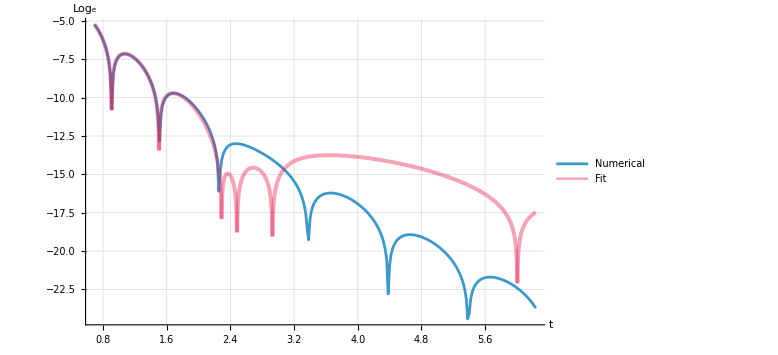

```mathematica
Show[ListPlot[Datag3Log,PlotStyle->PointSize[0.01],PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large,Joined->True],Plot[A0d15FitResgWr3[t]//Abs//Log,{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.4],RGBColor[0.9,.1,0.3]}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

### A=0.2

```mathematica
FileName="BB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d2";
FolderName="home/giulio/University/PhD/Simulations/";
TypeOfFile="bulk";
init=0;
end=3000;
each=5;
FNames=Table[StringJoin[TypeOfFile<>"_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
Name1=Table[StringJoin["/"<>FolderName<>FileName<>"/",
FNames[[i]],".h5"],{i,FNames//Length}];
dt=Import[Name1[[-1]],"Attributes"][[3,1]];
Timing[Obj=Module[{lastValid},Table[If[FileExistsQ[Name1[[i]]],lastValid=Import[Name1[[i]],"Data"];
lastValid,lastValid (*reuse previous if missing*)],{i,1,Length[Name1]}]];
(*Obj=Table[Import[Name1[[i]],"Data"](*[[1]]*),{i,1,Name1//Length}]*)];//AbsoluteTiming
Print["you have imported: "<>ToString[FNames//Length]<>" snapshot"];
(*"/home/giulio/University/PhD/JeccoGt2/examples/BB_QNM_1D_4p1_Vchannel_xpert/"*)
Print["defining times vector ..."]
times=Table[tim dt each+init dt,{tim,1,Obj//Length}];
(*snapshots=Table[(tim-1)  each+init ,{tim,1,Obj//Length}];*)
nt=times//Length;
Print["dt = "<>ToString[dt]]
Print["final time = "<>ToString[Import[Name1[[-1]],"Attributes"][[3,2]]//FullForm]]
```

{338.674,Null}

you have imported: 601 snapshot

defining times vector ...

dt = 0.00363636

final time = 10.909090909091276`

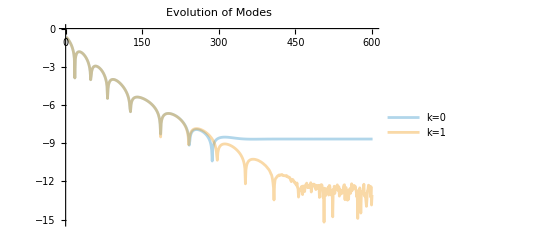

```mathematica
(*Parameters-Adjust these to match your simulation setup*)
g3=Obj[[;;,4,1,1,-1]];
(*4. Visualization*)
(*Plot the real part (oscillations) and the Magnitude (decay)*)
ListLinePlot[{(Re[g3])//Abs//Log[10,#]&,(Re[g3])-Re[g3[[-1]]]//Abs//Log[10,#]&},PlotRange->All,FrameLabel->{"Time Index","Amplitude"},PlotLabel->"Evolution of Modes",ImageSize->Full,PlotLegends->Placed[{"k=0","k=1","k=2","k=3","k=4","k=5"},{Right,Top}],PlotStyle->{Opacity[0.4]}]
```

```mathematica
0.1^4
```

0.0001

```mathematica
aaa=8;
bbb=83;
Timess=times;(*Table[(*dt*)dt (each i),{i,0,g3[[;;,1,1]]//Length}];*)
Lastg3=g3[[-1]];
Datag3=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*-Lastg3*)(*Lastg3[[1,1]]*))(*//Abs//Log*)}];
Datag3Log=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*Lastg3*))//Abs//Log}];
```

```mathematica
A0d2FitResgWr=NonlinearModelFit[Datag3,(*-wi (t-t0)+A1*)(*0.05 E^(-wi (t-t0))Cos[wr (t-t0)+ϕ]*)0.2 E^(-wi1(t-t01))Cos[wr1(t-t01)+ϕ1]/.wi1->Im[-ω1ot]/.wr1->Re[ω1ot](*+A2 Exp[-wi2(t-t01)]Cos[wr2(t-t01)+ϕ2]*)(*+A2 +wi2(t-t01)*)(*+ 0.1 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w1i (t-t0))Cos[w1r (t-t0)+ϕ1]+*)(*A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0]*) (*A0oft[t]*)(*+a1g  E^(-w1gi (t))Cos[w1gr (t-t0)+ϕ1g]*)(*+a2g E^(-w2gi (t-t0))Cos[ w2gr (t-t0)+ϕ2g] *)
,{{A1},ϕ1,{wi1,5.3},{wr1,4.8},t01(*,{A2},ϕ2,{wi2},{wr2},t02*)},{t(*,Timess[[aaa]],Timess[[bbb]]*)},MaxIterations->5000,ConfidenceLevel->0.9999999999];
```

```mathematica
A0d2FitResgWr["BestFitParameters"]
```

{A1→1.,ϕ1→6.30899,wi1→5.3,wr1→4.8,t01→0.0195779}

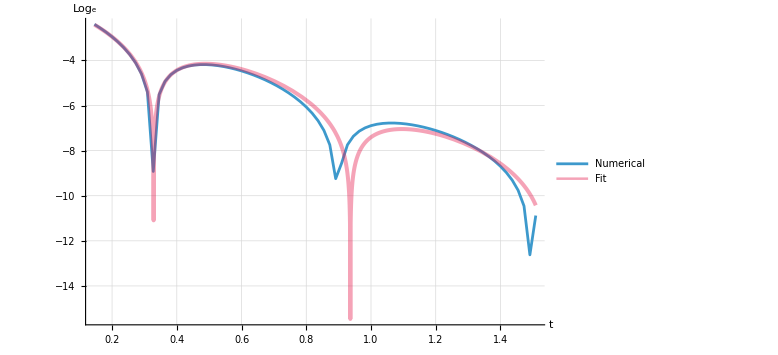

```mathematica
Show[ListPlot[Datag3Log,PlotStyle->PointSize[0.01],PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large,Joined->True],Plot[A0d2FitResgWr[t]//Abs//Log,{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.4],RGBColor[0.9,.1,0.3]}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

```mathematica
ClearAll[t];
aaa=260;
bbb=363;
Timess=times;(*Table[(*dt*)dt (each i),{i,0,g3[[;;,1,1]]//Length}];*)
Datag3=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*-Lastg3*)(*Lastg3[[1,1]]*))(*//Abs//Log*)}];
Datag3Log=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*Lastg3*))//Abs//Log}];
A0d2FitResgWr2=NonlinearModelFit[Datag3,(*-wi (t-t0)+A1*)A2 E^(-wi2 (t-t01))Cos[wr2 (t-t01)+ϕ2]/.A0d2FitResgWr["BestFitParameters"]/.wi1->Im[-ωfund]/.wr1->Re[ωfund](*//Abs//Log*)(*+ 0.1 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w1i (t-t0))Cos[w1r (t-t0)+ϕ1]+*)(*A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0]*) (*A0oft[t]*)(*+a1g  E^(-w1gi (t))Cos[w1gr (t-t0)+ϕ1g]*)(*+a2g E^(-w2gi (t-t0))Cos[ w2gr (t-t0)+ϕ2g] *)
,{(*a1g,a2g,A2,A0,ϕ1g,ϕ2g,w1gi,w1gr,w2gi,w2gr,ϕ2,ϕ0,*)A2,ϕ2,t02,wi2,wr2},{t(*,Timess[[aaa]],Timess[[bbb]]*)},MaxIterations->5000,ConfidenceLevel->0.9999999999];
```

```mathematica
A0d2FitResgWr2["BestFitParameters"]
A0d2FitResgWr["BestFitParameters"]
```

{A2→0.00646494,ϕ2→-8.91304,t02→1.,wi2→2.7488,wr2→3.11986}

{A1→1.,ϕ1→6.30899,wi1→5.3,wr1→4.8,t01→0.0195779}

```mathematica
0.2^3
```

0.008

```mathematica
0.15^3
```

0.003375

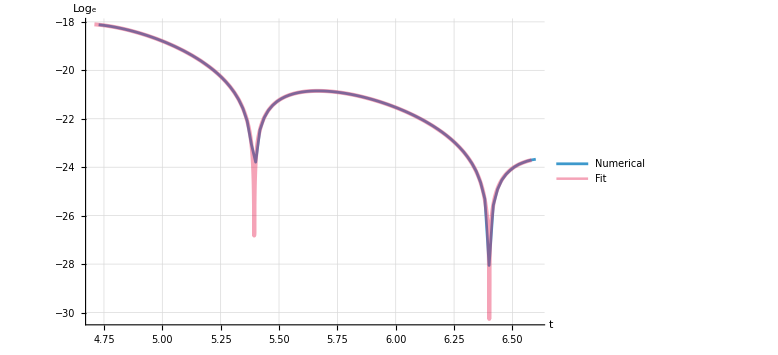

```mathematica
Timess=Table[(*dt*)dt (each i),{i,0,Obj//Length}];
Show[ListPlot[Datag3Log,PlotStyle->PointSize[0.01],PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large,Joined->True],Plot[A0d2FitResgWr2[t]//Abs//Log,{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.4],RGBColor[0.9,.1,0.3]}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

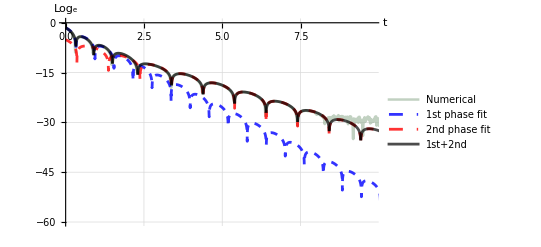

```mathematica
Show[ListPlot[Transpose[{Timess[[;;-2]],(g3[[;;]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*Lastg3*))//Abs//Log}],PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.6],RGBColor[0.6,0.7,0.6]},PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Full,Joined->True],Plot[A0d2FitResgWr[t]//Abs//Log,{t,Timess[[1]],Timess[[-1]]},PlotLegends->{"1st phase fit"},PlotStyle->{Blue,Opacity[0.8],Dashed},PlotLegends->Placed["Numerical", {Center}]],Plot[A0d2FitResgWr2[t]//Abs//Log,{t,Timess[[1]],Timess[[-1]]},PlotLegends->{"2nd phase fit"},PlotStyle->{Red,Opacity[0.8],Dashed}],Plot[A0d2FitResgWr[t]+A0d2FitResgWr2[t]//Abs//Log,{t,Timess[[1]],Timess[[-1]]},PlotLegends->{"1st+2nd"},PlotStyle->{Black,Opacity[0.7],Point}],PlotRange->{{0,9.8},{-60,0.1}},AxesLabel->{"t","Log_e"}]
```

```mathematica
Export["/home/giulio/Pictures/Jecco_QNM_gxy"<>FileName<>".pdf",%]
```

/home/giulio/Pictures/Jecco_QNM_gxyBB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d2.pdf

```mathematica
aaa=38;
bbb=343;
Timess=times;(*Table[(*dt*)dt (each i),{i,0,g3[[;;,1,1]]//Length}];*)
Datag3=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*-Lastg3*)(*Lastg3[[1,1]]*))(*//Abs//Log*)}];
Datag3Log=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*Lastg3*))//Abs//Log}];
```

```mathematica
A0d2FitResgWr3=NonlinearModelFit[Datag3,(*-wi (t-t0)+A1*)(*0.05 E^(-wi (t-t0))Cos[wr (t-t0)+ϕ]*)0.2 E^(-wi1(t-t01))Cos[wr1(t-t01)+ϕ1]+A2 Exp[-wi2(t-t01)]Cos[wr2(t-t01)+ϕ2](*/.A0d15FitResgWr["BestFitParameters"][[3;;4]]*)/.A0d2FitResgWr2["BestFitParameters"][[4;;5]](*+A2 +wi2(t-t01)*)(*+ 0.1 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w1i (t-t0))Cos[w1r (t-t0)+ϕ1]+*)(*A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0]*) (*A0oft[t]*)(*+a1g  E^(-w1gi (t))Cos[w1gr (t-t0)+ϕ1g]*)(*+a2g E^(-w2gi (t-t0))Cos[ w2gr (t-t0)+ϕ2g] *)
,{{A1,0.00015},ϕ1,{wi1,A0d15FitResgWr["BestFitParameters"][[3,2]]},{wr1,A0d15FitResgWr["BestFitParameters"][[4,2]]},{t01,0.001},{A2,0.0001},ϕ2,{wi2,A0d15FitResgWr2["BestFitParameters"][[4,2]]},{wr2,A0d15FitResgWr2["BestFitParameters"][[5,2]]},t02},{t(*,Timess[[aaa]],Timess[[bbb]]*)},MaxIterations->5000,ConfidenceLevel->0.9999999999];
```

```mathematica
A0d2FitResgWr3["BestFitParameters"]
```

{A1→0.00015,ϕ1→0.00789757,wi1→4.78346,wr1→5.15438,t01→0.0209102,A2→0.00641149,ϕ2→22.5152,wi2→1.,wr2→1.,t02→1.}

```mathematica
A0d2FitResgWr["BestFitParameters"]
A0d2FitResgWr2["BestFitParameters"]
```

{A1→1.,ϕ1→6.30899,wi1→5.3,wr1→4.8,t01→0.0195779}

{A2→0.00646494,ϕ2→-8.91304,t02→1.,wi2→2.7488,wr2→3.11986}

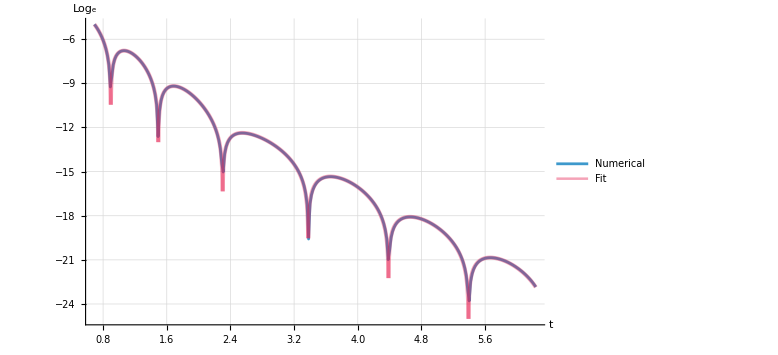

```mathematica
Show[ListPlot[Datag3Log,PlotStyle->PointSize[0.01],PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large,Joined->True],Plot[A0d2FitResgWr3[t]//Abs//Log,{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.4],RGBColor[0.9,.1,0.3]}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

### A=0.25

```mathematica
FileName="BB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d25";
FolderName="home/giulio/University/PhD/Simulations/";
TypeOfFile="bulk";
init=0;
end=3000;
each=5;
FNames=Table[StringJoin[TypeOfFile<>"_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
Name1=Table[StringJoin["/"<>FolderName<>FileName<>"/",
FNames[[i]],".h5"],{i,FNames//Length}];
dt=Import[Name1[[-1]],"Attributes"][[3,1]];
Timing[Obj=Module[{lastValid},Table[If[FileExistsQ[Name1[[i]]],lastValid=Import[Name1[[i]],"Data"];
lastValid,lastValid (*reuse previous if missing*)],{i,1,Length[Name1]}]];
(*Obj=Table[Import[Name1[[i]],"Data"](*[[1]]*),{i,1,Name1//Length}]*)];//AbsoluteTiming
Print["you have imported: "<>ToString[FNames//Length]<>" snapshot"];
(*"/home/giulio/University/PhD/JeccoGt2/examples/BB_QNM_1D_4p1_Vchannel_xpert/"*)
Print["defining times vector ..."]
times=Table[tim dt each+init dt,{tim,1,Obj//Length}];
(*snapshots=Table[(tim-1)  each+init ,{tim,1,Obj//Length}];*)
nt=times//Length;
Print["dt = "<>ToString[dt]]
Print["final time = "<>ToString[Import[Name1[[-1]],"Attributes"][[3,2]]//FullForm]]
```

{18.8922,Null}

you have imported: 601 snapshot

defining times vector ...

dt = 0.00363636

final time = 10.909090909091276`

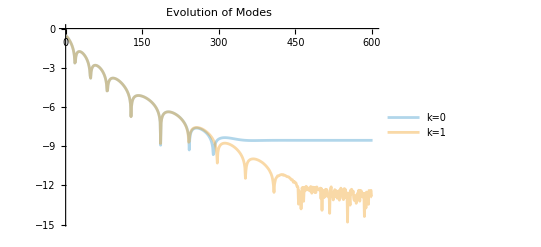

```mathematica
(*Parameters-Adjust these to match your simulation setup*)
g3=Obj[[;;,4,1,1,-1]];
(*4. Visualization*)
(*Plot the real part (oscillations) and the Magnitude (decay)*)
ListLinePlot[{(Re[g3])//Abs//Log[10,#]&,(Re[g3])-Re[g3[[-1]]]//Abs//Log[10,#]&},PlotRange->All,FrameLabel->{"Time Index","Amplitude"},PlotLabel->"Evolution of Modes",ImageSize->Full,PlotLegends->Placed[{"k=0","k=1","k=2","k=3","k=4","k=5"},{Right,Top}],PlotStyle->{Opacity[0.4]}]
```

```mathematica
0.1^4
```

0.0001

```mathematica
aaa=8;
bbb=80;
Timess=times;(*Table[(*dt*)dt (each i),{i,0,g3[[;;,1,1]]//Length}];*)
Lastg3=g3[[-1]];
Datag3=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*-Lastg3*)(*Lastg3[[1,1]]*))(*//Abs//Log*)}];
Datag3Log=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*Lastg3*))//Abs//Log}];
```

```mathematica
A0d25FitResgWr=NonlinearModelFit[Datag3,(*-wi (t-t0)+A1*)(*0.05 E^(-wi (t-t0))Cos[wr (t-t0)+ϕ]*)0.25 E^(-wi1(t-t01))Cos[wr1(t-t01)+ϕ1]/.wi1->Im[-ω1ot]/.wr1->Re[ω1ot](*+A2 Exp[-wi2(t-t01)]Cos[wr2(t-t01)+ϕ2]*)(*+A2 +wi2(t-t01)*)(*+ 0.1 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w1i (t-t0))Cos[w1r (t-t0)+ϕ1]+*)(*A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0]*) (*A0oft[t]*)(*+a1g  E^(-w1gi (t))Cos[w1gr (t-t0)+ϕ1g]*)(*+a2g E^(-w2gi (t-t0))Cos[ w2gr (t-t0)+ϕ2g] *)
,{{A1},ϕ1,{wi1,5.2},{wr1,4.8},t01(*,{A2},ϕ2,{wi2},{wr2},t02*)},{t(*,Timess[[aaa]],Timess[[bbb]]*)},MaxIterations->5000,ConfidenceLevel->0.9999999999];
```

```mathematica
A0d25FitResgWr["BestFitParameters"]
```

{A1→1.,ϕ1→6.36233,wi1→5.2,wr1→4.8,t01→0.0186479}

```mathematica
A0d2FitResgWr["BestFitParameters"]
```

{A1→1.,ϕ1→6.30899,wi1→5.3,wr1→4.8,t01→0.0195779}

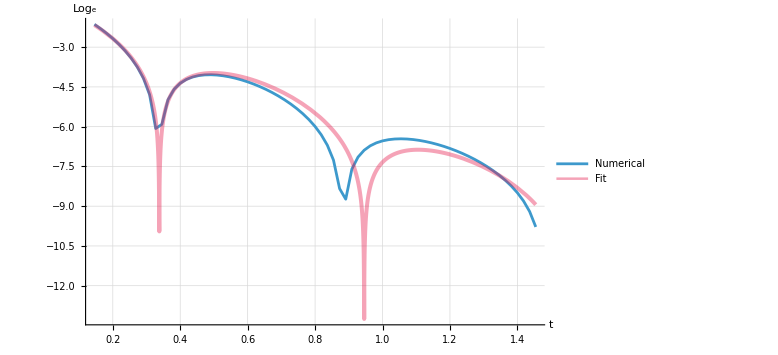

```mathematica
Show[ListPlot[Datag3Log,PlotStyle->PointSize[0.01],PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large,Joined->True],Plot[A0d25FitResgWr[t]//Abs//Log,{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.4],RGBColor[0.9,.1,0.3]}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

```mathematica
ClearAll[t];
aaa=290;
bbb=400;
Timess=times;(*Table[(*dt*)dt (each i),{i,0,g3[[;;,1,1]]//Length}];*)
Datag3=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*-Lastg3*)(*Lastg3[[1,1]]*))(*//Abs//Log*)}];
Datag3Log=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*Lastg3*))//Abs//Log}];
A0d25FitResgWr2=NonlinearModelFit[Datag3,(*-wi (t-t0)+A1*)A2 E^(-wi2 (t-t01))Cos[wr2 (t-t01)+ϕ2](*+A3 E^(-wi2 (t-t01))Cos[-wr2 (t-t01)+ϕ3]*)/.A0d25FitResgWr["BestFitParameters"]/.wi1->Im[-ωfund]/.wr1->Re[ωfund](*//Abs//Log*)(*+ 0.1 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w1i (t-t0))Cos[w1r (t-t0)+ϕ1]+*)(*A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0]*) (*A0oft[t]*)(*+a1g  E^(-w1gi (t))Cos[w1gr (t-t0)+ϕ1g]*)(*+a2g E^(-w2gi (t-t0))Cos[ w2gr (t-t0)+ϕ2g] *)
,{(*a1g,a2g,A2,A0,ϕ1g,ϕ2g,w1gi,w1gr,w2gi,w2gr,ϕ2,ϕ0,*)A2,ϕ2,t02,wi2,wr2,A3,ϕ3},{t(*,Timess[[aaa]],Timess[[bbb]]*)},MaxIterations->5000,ConfidenceLevel->0.9999999999];
```

```mathematica
A0d25FitResgWr2["BestFitParameters"]
```

{A2→-0.0125434,ϕ2→-5.77886,t02→1.,wi2→2.74604,wr2→3.11913,A3→1.,ϕ3→1.}

```mathematica
0.25^3
```

0.015625

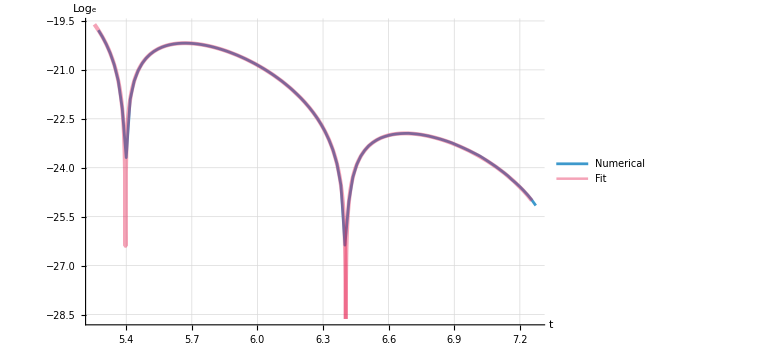

```mathematica
Timess=Table[(*dt*)dt (each i),{i,0,Obj//Length}];
Show[ListPlot[Datag3Log,PlotStyle->PointSize[0.01],PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large,Joined->True],Plot[A0d25FitResgWr2[t]//Abs//Log,{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.4],RGBColor[0.9,.1,0.3]}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

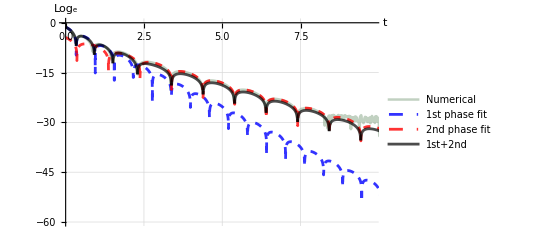

```mathematica
Show[ListPlot[Transpose[{Timess[[;;-2]],(g3[[;;]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*Lastg3*))//Abs//Log}],PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.6],RGBColor[0.6,0.7,0.6]},PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Full,Joined->True],Plot[A0d25FitResgWr[t]//Abs//Log,{t,Timess[[1]],Timess[[-1]]},PlotLegends->{"1st phase fit"},PlotStyle->{Blue,Opacity[0.8],Dashed},PlotLegends->Placed["Numerical", {Center}]],Plot[A0d25FitResgWr2[t]//Abs//Log,{t,Timess[[1]],Timess[[-1]]},PlotLegends->{"2nd phase fit"},PlotStyle->{Red,Opacity[0.8],Dashed}],Plot[A0d25FitResgWr[t]+A0d2FitResgWr2[t]//Abs//Log,{t,Timess[[1]],Timess[[-1]]},PlotLegends->{"1st+2nd"},PlotStyle->{Black,Opacity[0.7],Point}],PlotRange->{{0,9.8},{-60,0.1}},AxesLabel->{"t","Log_e"}]
```

```mathematica
Export["/home/giulio/Pictures/Jecco_QNM_gxy"<>FileName<>".pdf",%]
```

/home/giulio/Pictures/Jecco_QNM_gxyBB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d25.pdf

```mathematica
aaa=38;
bbb=343;
Timess=times;(*Table[(*dt*)dt (each i),{i,0,g3[[;;,1,1]]//Length}];*)
Datag3=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*-Lastg3*)(*Lastg3[[1,1]]*))(*//Abs//Log*)}];
Datag3Log=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*Lastg3*))//Abs//Log}];
```

```mathematica
A0d2FitResgWr3=NonlinearModelFit[Datag3,(*-wi (t-t0)+A1*)(*0.05 E^(-wi (t-t0))Cos[wr (t-t0)+ϕ]*)0.2 E^(-wi1(t-t01))Cos[wr1(t-t01)+ϕ1]+A2 Exp[-wi2(t-t01)]Cos[wr2(t-t01)+ϕ2](*/.A0d15FitResgWr["BestFitParameters"][[3;;4]]*)/.A0d2FitResgWr2["BestFitParameters"][[4;;5]](*+A2 +wi2(t-t01)*)(*+ 0.1 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w1i (t-t0))Cos[w1r (t-t0)+ϕ1]+*)(*A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0]*) (*A0oft[t]*)(*+a1g  E^(-w1gi (t))Cos[w1gr (t-t0)+ϕ1g]*)(*+a2g E^(-w2gi (t-t0))Cos[ w2gr (t-t0)+ϕ2g] *)
,{{A1,0.00015},ϕ1,{wi1,A0d15FitResgWr["BestFitParameters"][[3,2]]},{wr1,A0d15FitResgWr["BestFitParameters"][[4,2]]},{t01,0.001},{A2,0.0001},ϕ2,{wi2,A0d15FitResgWr2["BestFitParameters"][[4,2]]},{wr2,A0d15FitResgWr2["BestFitParameters"][[5,2]]},t02},{t(*,Timess[[aaa]],Timess[[bbb]]*)},MaxIterations->5000,ConfidenceLevel->0.9999999999];
```

```mathematica
A0d2FitResgWr3["BestFitParameters"]
```

{A1→0.00015,ϕ1→0.209808,wi1→4.79597,wr1→5.14546,t01→0.0664949,A2→-0.0111216,ϕ2→57.2087,wi2→1.,wr2→1.,t02→1.}

```mathematica
A0d2FitResgWr["BestFitParameters"]
A0d2FitResgWr2["BestFitParameters"]
```

{A1→1.,ϕ1→6.30899,wi1→5.3,wr1→4.8,t01→0.0195779}

{A2→0.00646494,ϕ2→-8.91304,t02→1.,wi2→2.7488,wr2→3.11986}

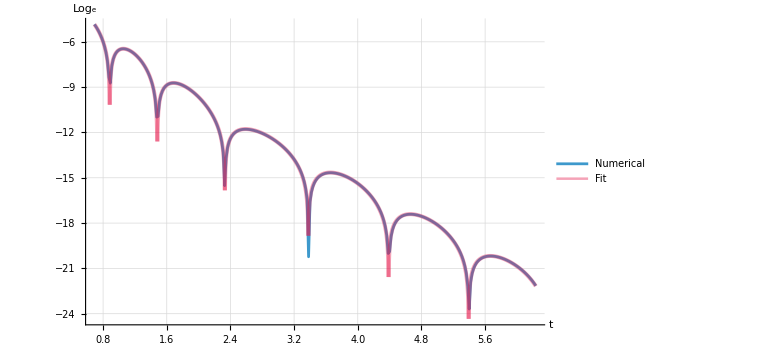

```mathematica
Show[ListPlot[Datag3Log,PlotStyle->PointSize[0.01],PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large,Joined->True],Plot[A0d2FitResgWr3[t]//Abs//Log,{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.4],RGBColor[0.9,.1,0.3]}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

### A=0.3

```mathematica
FileName="BB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d3";
FolderName="home/giulio/University/PhD/Simulations/";
TypeOfFile="bulk";
init=0;
end=3000;
each=10;
FNames=Table[StringJoin[TypeOfFile<>"_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
Name1=Table[StringJoin["/"<>FolderName<>FileName<>"/",
FNames[[i]],".h5"],{i,FNames//Length}];
dt=Import[Name1[[-1]],"Attributes"][[3,1]];
Timing[Obj=Module[{lastValid},Table[If[FileExistsQ[Name1[[i]]],lastValid=Import[Name1[[i]],"Data"];
lastValid,lastValid (*reuse previous if missing*)],{i,1,Length[Name1]}]];
(*Obj=Table[Import[Name1[[i]],"Data"](*[[1]]*),{i,1,Name1//Length}]*)];//AbsoluteTiming
Print["you have imported: "<>ToString[FNames//Length]<>" snapshot"];
(*"/home/giulio/University/PhD/JeccoGt2/examples/BB_QNM_1D_4p1_Vchannel_xpert/"*)
Print["defining times vector ..."]
times=Table[tim dt each+init dt,{tim,1,Obj//Length}];
(*snapshots=Table[(tim-1)  each+init ,{tim,1,Obj//Length}];*)
nt=times//Length;
Print["dt = "<>ToString[dt]]
Print["final time = "<>ToString[Import[Name1[[-1]],"Attributes"][[3,2]]//FullForm]]
```

{9.55287,Null}

you have imported: 301 snapshot

defining times vector ...

dt = 0.00363636

final time = 10.909090909091276`

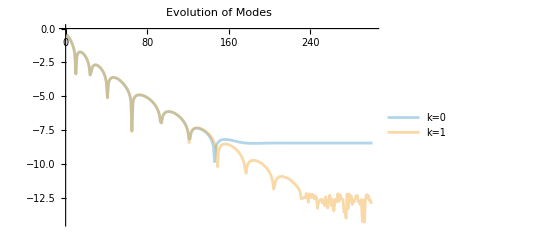

```mathematica
(*Parameters-Adjust these to match your simulation setup*)
g3=Obj[[;;,4,1,1,-1]];
(*4. Visualization*)
(*Plot the real part (oscillations) and the Magnitude (decay)*)
ListLinePlot[{(Re[g3])//Abs//Log[10,#]&,(Re[g3])-Re[g3[[-1]]]//Abs//Log[10,#]&},PlotRange->All,FrameLabel->{"Time Index","Amplitude"},PlotLabel->"Evolution of Modes",ImageSize->Full,PlotLegends->Placed[{"k=0","k=1","k=2","k=3","k=4","k=5"},{Right,Top}],PlotStyle->{Opacity[0.4]}]
```

```mathematica
0.1^4
```

0.0001

```mathematica
aaa=7;
bbb=36;
Timess=times;(*Table[(*dt*)dt (each i),{i,0,g3[[;;,1,1]]//Length}];*)
Lastg3=g3[[-1]];
Datag3=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*-Lastg3*)(*Lastg3[[1,1]]*))(*//Abs//Log*)}];
Datag3Log=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*Lastg3*))//Abs//Log}];
```

```mathematica
A0d3FitResgWr=NonlinearModelFit[Datag3,(*-wi (t-t0)+A1*)(*0.05 E^(-wi (t-t0))Cos[wr (t-t0)+ϕ]*)0.3 E^(-wi1(t-t01))Cos[wr1(t-t01)+ϕ1]/.wi1->Im[-ω1ot]/.wr1->Re[ω1ot](*+A2 Exp[-wi2(t-t01)]Cos[wr2(t-t01)+ϕ2]*)(*+A2 +wi2(t-t01)*)(*+ 0.1 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w1i (t-t0))Cos[w1r (t-t0)+ϕ1]+*)(*A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0]*) (*A0oft[t]*)(*+a1g  E^(-w1gi (t))Cos[w1gr (t-t0)+ϕ1g]*)(*+a2g E^(-w2gi (t-t0))Cos[ w2gr (t-t0)+ϕ2g] *)
,{{A1},ϕ1,{wi1,4.955091289557959},{wr1,5.392238705862567},t01(*,{A2},ϕ2,{wi2},{wr2},t02*)},{t(*,Timess[[aaa]],Timess[[bbb]]*)},MaxIterations->5000,ConfidenceLevel->0.9999999999];
```

```mathematica
A0d3FitResgWr["BestFitParameters"]
```

{A1→1.,ϕ1→6.5324,wi1→4.95509,wr1→5.39224,t01→0.0175313}

```mathematica
ω1ot
```

-5.169520975762229549404618858897224991945721855354884116-4.763570116920460863645146483709052189501385495221501904 ⅈ

```mathematica
A0d2FitResgWr["BestFitParameters"]
```

{A1→1.,ϕ1→6.30899,wi1→5.3,wr1→4.8,t01→0.0195779}

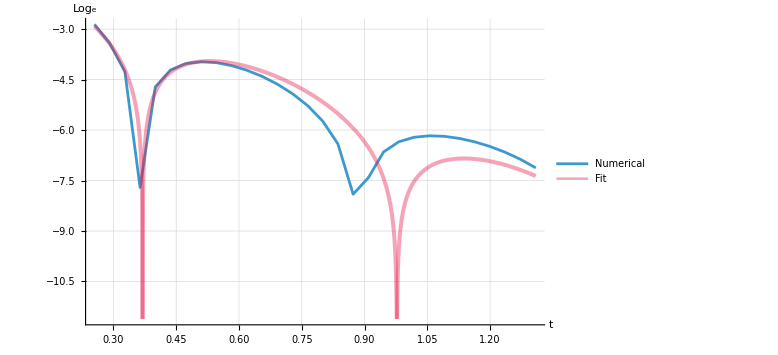

```mathematica
Show[ListPlot[Datag3Log,PlotStyle->PointSize[0.01],PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large,Joined->True],Plot[A0d3FitResgWr[t]//Abs//Log,{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.4],RGBColor[0.9,.1,0.3]}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

```mathematica
ClearAll[t];
aaa=90;
bbb=200;
Timess=times;(*Table[(*dt*)dt (each i),{i,0,g3[[;;,1,1]]//Length}];*)
Datag3=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*-Lastg3*)(*Lastg3[[1,1]]*))(*//Abs//Log*)}];
Datag3Log=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*Lastg3*))//Abs//Log}];
A0d3FitResgWr2=NonlinearModelFit[Datag3,(*-wi (t-t0)+A1*)A2 E^(-wi2 (t-t01))Cos[wr2 (t-t01)+ϕ2]/.wi2->Im[-ωfund]/.wr2->Re[-ωfund](*+A3 E^(-wi2 (t-t01))Cos[-wr2 (t-t01)+ϕ3]*)/.A0d3FitResgWr["BestFitParameters"](*//Abs//Log*)(*+ 0.1 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w1i (t-t0))Cos[w1r (t-t0)+ϕ1]+*)(*A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0]*) (*A0oft[t]*)(*+a1g  E^(-w1gi (t))Cos[w1gr (t-t0)+ϕ1g]*)(*+a2g E^(-w2gi (t-t0))Cos[ w2gr (t-t0)+ϕ2g] *)
,{(*a1g,a2g,A2,A0,ϕ1g,ϕ2g,w1gi,w1gr,w2gi,w2gr,ϕ2,ϕ0,*)A2,ϕ2,t02,wi2,wr2,A3,ϕ3},{t(*,Timess[[aaa]],Timess[[bbb]]*)},MaxIterations->5000,ConfidenceLevel->0.9999999999];
```

```mathematica
A0d3FitResgWr2["BestFitParameters"]
A0d15FitResgWr2["BestFitParameters"]
```

{A2→-0.0227347,ϕ2→-0.44272,t02→1.,wi2→1.,wr2→1.,A3→1.,ϕ3→1.}

{A2→-0.00277611,ϕ2→0.492435,t01→1.,wi2→1.,wr2→1.}

```mathematica
0.25^3
```

0.015625

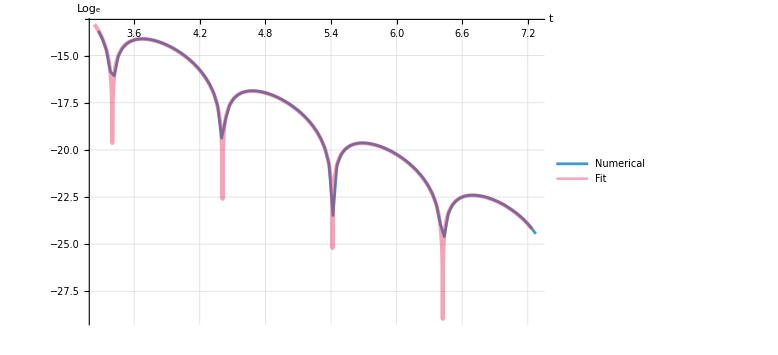

```mathematica
Timess=Table[(*dt*)dt (each i),{i,0,Obj//Length}];
Show[ListPlot[Datag3Log,PlotStyle->PointSize[0.01],PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large,Joined->True],Plot[A0d3FitResgWr2[t]//Abs//Log,{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.4],RGBColor[0.9,.1,0.3]}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

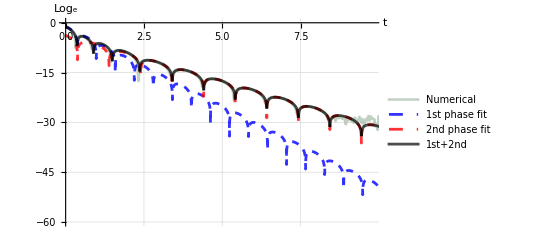

```mathematica
Show[ListPlot[Transpose[{Timess[[;;-2]],(g3[[;;]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*Lastg3*))//Abs//Log}],PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.6],RGBColor[0.6,0.7,0.6]},PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Full,Joined->True],Plot[A0d3FitResgWr[t]//Abs//Log,{t,Timess[[1]],Timess[[-1]]},PlotLegends->{"1st phase fit"},PlotStyle->{Blue,Opacity[0.8],Dashed},PlotLegends->Placed["Numerical", {Center}]],Plot[A0d3FitResgWr2[t]//Abs//Log,{t,Timess[[1]],Timess[[-1]]},PlotLegends->{"2nd phase fit"},PlotStyle->{Red,Opacity[0.8],Dashed}],Plot[A0d3FitResgWr[t]+A0d3FitResgWr2[t]//Abs//Log,{t,Timess[[1]],Timess[[-1]]},PlotLegends->{"1st+2nd"},PlotStyle->{Black,Opacity[0.7],Point}],PlotRange->{{0,9.8},{-60,0.1}},AxesLabel->{"t","Log_e"}]
```

```mathematica
Export["/home/giulio/Pictures/Jecco_QNM_gxy"<>FileName<>".pdf",%]
```

/home/giulio/Pictures/Jecco_QNM_gxyBB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d3.pdf

```mathematica
aaa=38;
bbb=343;
Timess=times;(*Table[(*dt*)dt (each i),{i,0,g3[[;;,1,1]]//Length}];*)
Datag3=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*-Lastg3*)(*Lastg3[[1,1]]*))(*//Abs//Log*)}];
Datag3Log=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*Lastg3*))//Abs//Log}];
```

Part::take: Cannot take positions 38 through 343 in {0.0363636,0.0727273,0.109091,0.145455,0.181818,0.218182,0.254545,0.290909,0.327273,0.363636,0.4,0.436364,0.472727,«25»,1.41818,1.45455,1.49091,1.52727,1.56364,1.6,1.63636,1.67273,1.70909,1.74545,1.78182,1.81818,«251»}.

Part::take: Cannot take positions 38 through 343 in {0.348032,0.284175,0.224931,0.172151,0.126628,0.0884772,0.0573913,0.0328286,0.014102,0.000450731,-0.00891682,-0.0147822,«28»,-7.83326×10^-6,-0.0000938233,-0.000157673,-0.000202107,-0.000229994,-0.000244187,-0.000247395,-0.000242093,-0.000230473,-0.000214425,«251»}.

Part::take: Cannot take positions 38 through 343 in {0.0363636,0.0727273,0.109091,0.145455,0.181818,0.218182,0.254545,0.290909,0.327273,0.363636,0.4,0.436364,0.472727,«25»,1.41818,1.45455,1.49091,1.52727,1.56364,1.6,1.63636,1.67273,1.70909,1.74545,1.78182,1.81818,«251»}.

Part::take: Cannot take positions 38 through 343 in {0.348032,0.284175,0.224931,0.172151,0.126628,0.0884772,0.0573913,0.0328286,0.014102,0.000450731,-0.00891682,-0.0147822,«28»,-7.83326×10^-6,-0.0000938233,-0.000157673,-0.000202107,-0.000229994,-0.000244187,-0.000247395,-0.000242093,-0.000230473,-0.000214425,«251»}.

```mathematica
A0d2FitResgWr3=NonlinearModelFit[Datag3,(*-wi (t-t0)+A1*)(*0.05 E^(-wi (t-t0))Cos[wr (t-t0)+ϕ]*)0.2 E^(-wi1(t-t01))Cos[wr1(t-t01)+ϕ1]+A2 Exp[-wi2(t-t01)]Cos[wr2(t-t01)+ϕ2](*/.A0d15FitResgWr["BestFitParameters"][[3;;4]]*)/.A0d2FitResgWr2["BestFitParameters"][[4;;5]](*+A2 +wi2(t-t01)*)(*+ 0.1 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w1i (t-t0))Cos[w1r (t-t0)+ϕ1]+*)(*A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0]*) (*A0oft[t]*)(*+a1g  E^(-w1gi (t))Cos[w1gr (t-t0)+ϕ1g]*)(*+a2g E^(-w2gi (t-t0))Cos[ w2gr (t-t0)+ϕ2g] *)
,{{A1,0.00015},ϕ1,{wi1,A0d15FitResgWr["BestFitParameters"][[3,2]]},{wr1,A0d15FitResgWr["BestFitParameters"][[4,2]]},{t01,0.001},{A2,0.0001},ϕ2,{wi2,A0d15FitResgWr2["BestFitParameters"][[4,2]]},{wr2,A0d15FitResgWr2["BestFitParameters"][[5,2]]},t02},{t(*,Timess[[aaa]],Timess[[bbb]]*)},MaxIterations->5000,ConfidenceLevel->0.9999999999];
```

NonlinearModelFit::nrlnum: The function value {0.000882879-1. Optimization`FindFit`y$240349,-1.71479×10^-6-1. Optimization`FindFit`y$240349} is not a list of real numbers with dimensions {2} at {A1,ϕ1,wi1,wr1,t01,A2,ϕ2,wi2,wr2,t02} = {0.00015,1.,5.3,4.8,0.001,0.0001,1.,1.,1.,1.}.

NonlinearModelFit::nrlnum: The function value {0.000882879-1. Optimization`FindFit`y$240370,-1.71479×10^-6-1. Optimization`FindFit`y$240370} is not a list of real numbers with dimensions {2} at {A1,ϕ1,wi1,wr1,t01,A2,ϕ2,wi2,wr2,t02} = {0.00015,1.,5.3,4.8,0.001,0.0001,1.,1.,1.,1.}.

```mathematica
A0d2FitResgWr3["BestFitParameters"]
```

NonlinearModelFit::nrlnum: The function value {0.000882879-1. Optimization`FindFit`y$240388,-1.71479×10^-6-1. Optimization`FindFit`y$240388} is not a list of real numbers with dimensions {2} at {A1,ϕ1,wi1,wr1,t01,A2,ϕ2,wi2,wr2,t02} = {0.00015,1.,5.3,4.8,0.001,0.0001,1.,1.,1.,1.}.

NonlinearModelFit[{{0.0363636,0.0727273,0.109091,0.145455,0.181818,0.218182,0.254545,0.290909,0.327273,0.363636,0.4,0.436364,0.472727,0.509091,0.545455,0.581818,0.618182,0.654545,0.690909,0.727273,0.763636,0.8,0.836364,0.872727,0.909091,0.945455,0.981818,1.01818,1.05455,1.09091,1.12727,1.16364,1.2,1.23636,1.27273,1.30909,1.34545,1.38182,1.41818,1.45455,1.49091,1.52727,1.56364,1.6,1.63636,1.67273,1.70909,1.74545,1.78182,1.81818,1.85455,1.89091,1.92727,1.96364,2.,2.03636,2.07273,2.10909,2.14545,2.18182,2.21818,2.25455,2.29091,2.32727,2.36364,2.4,2.43636,2.47273,2.50909,2.54545,2.58182,2.61818,2.65455,2.69091,2.72727,2.76364,2.8,2.83636,2.87273,2.90909,2.94545,2.98182,3.01818,3.05455,3.09091,3.12727,3.16364,3.2,3.23636,3.27273,3.30909,3.34545,3.38182,3.41818,3.45455,3.49091,3.52727,3.56364,3.6,3.63636,3.67273,3.70909,3.74545,3.78182,3.81818,3.85455,3.89091,3.92727,3.96364,4.,4.03636,4.07273,4.10909,4.14545,4.18182,4.21818,4.25455,4.29091,4.32727,4.36364,4.4,4.43636,4.47273,4.50909,4.54545,4.58182,4.61818,4.65455,4.69091,4.72727,4.76364,4.8,4.83636,4.87273,4.90909,4.94545,4.98182,5.01818,5.05455,5.09091,5.12727,5.16364,5.2,5.23636,5.27273,5.30909,5.34545,5.38182,5.41818,5.45455,5.49091,5.52727,5.56364,5.6,5.63636,5.67273,5.70909,5.74545,5.78182,5.81818,5.85455,5.89091,5.92727,5.96364,6.,6.03636,6.07273,6.10909,6.14545,6.18182,6.21818,6.25455,6.29091,6.32727,6.36364,6.4,6.43636,6.47273,6.50909,6.54545,6.58182,6.61818,6.65455,6.69091,6.72727,6.76364,6.8,6.83636,6.87273,6.90909,6.94545,6.98182,7.01818,7.05455,7.09091,7.12727,7.16364,7.2,7.23636,7.27273,7.30909,7.34545,7.38182,7.41818,7.45455,7.49091,7.52727,7.56364,7.6,7.63636,7.67273,7.70909,7.74545,7.78182,7.81818,7.85455,7.89091,7.92727,7.96364,8.,8.03636,8.07273,8.10909,8.14545,8.18182,8.21818,8.25455,8.29091,8.32727,8.36364,8.4,8.43636,8.47273,8.50909,8.54545,8.58182,8.61818,8.65455,8.69091,8.72727,8.76364,8.8,8.83636,8.87273,8.90909,8.94545,8.98182,9.01818,9.05455,9.09091,9.12727,9.16364,9.2,9.23636,9.27273,9.30909,9.34545,9.38182,9.41818,9.45455,9.49091,9.52727,9.56364,9.6,9.63636,9.67273,9.70909,9.74545,9.78182,9.81818,9.85455,9.89091,9.92727,9.96364,10.,10.0364,10.0727,10.1091,10.1455,10.1818,10.2182,10.2545,10.2909,10.3273,10.3636,10.4,10.4364,10.4727,10.5091,10.5455,10.5818,10.6182,10.6545,10.6909,10.7273,10.7636,10.8,10.8364,10.8727,10.9091,10.9455}⟦38;;343⟧,3.52453×10^-9+Re[{0.348032,0.284175,0.224931,0.172151,0.126628,0.0884772,0.0573913,0.0328286,0.014102,0.000450731,-0.00891682,-0.0147822,-0.0178833,-0.0188887,-0.0183824,-0.0168566,-0.014712,-0.0122638,-0.00974929,-0.00733859,-0.00514506,-0.00323595,-0.00164241,-0.000368451,0.000601345,0.00129518,0.00174873,0.00200102,0.00209132,0.00205683,0.00193129,0.00174415,0.00152017,0.00127939,0.00103741,0.000805806,0.00059262,0.000402919,0.000239347,0.000102656,-7.83326×10^-6,-0.0000938233,-0.000157673,-0.000202107,-0.000229994,-0.000244187,-0.000247395,-0.000242093,-0.000230473,-0.000214425,-0.000195534,-0.000175103,-0.000154163,-0.000133506,-0.000113715,-0.000095192,-0.0000781944,-0.0000628636,-0.0000492507,-0.0000373386,-0.000027061,-0.0000183178,-0.0000109875,-4.93681×10^-6,-2.85962×10^-8,3.87246×10^-6,6.89591×10^-6,9.16293×10^-6,0.0000107848,0.0000118623,0.0000124855,0.0000127345,0.0000126793,0.0000123813,0.0000118938,0.0000112626,0.0000105271,9.72086×10^-6,8.87213×10^-6,8.00467×10^-6,7.13814×10^-6,6.2886×10^-6,5.46891×10^-6,4.68914×10^-6,3.95689×10^-6,3.27758×10^-6,2.65478×10^-6,2.09041×10^-6,1.58504×10^-6,1.13803×10^-6,7.47811×10^-7,4.12009×10^-7,1.27646×10^-7,-1.08722×10^-7,-3.00859×10^-7,-4.52737×10^-7,-5.68421×10^-7,-6.51983×10^-7,-7.07419×10^-7,-7.38589×10^-7,-7.49164×10^-7,-7.42585×10^-7,-7.22036×10^-7,-6.90425×10^-7,-6.5037×10^-7,-6.04202×10^-7,-5.53962×10^-7,-5.01412×10^-7,-4.48049×10^-7,-3.95122×10^-7,-3.43643×10^-7,-2.94418×10^-7,-2.4806×10^-7,-2.05012×10^-7,-1.65569×10^-7,-1.29898×10^-7,-9.80584×10^-8,-7.00183×10^-8,-4.56731×10^-8,-2.48594×10^-8,-7.36989×10^-9,7.03338×10^-9,1.86107×10^-8,2.7633×10^-8,3.43766×10^-8,3.91141×10^-8,4.21108×10^-8,4.36197×10^-8,4.38792×10^-8,4.3111×10^-8,4.15161×10^-8,3.92784×10^-8,3.65606×10^-8,3.35054×10^-8,3.02384×10^-8,2.68652×10^-8,2.34743×10^-8,2.01393×10^-8,1.6919×10^-8,1.38595×10^-8,1.09951×10^-8,8.34936×10^-9,5.93731×10^-9,3.7665×10^-9,1.83859×10^-9,1.48522×10^-10,-1.31097×10^-9,-2.55228×10^-9,-3.58829×10^-9,-4.43611×10^-9,-5.111×10^-9,-5.63132×10^-9,-6.01337×10^-9,-6.27499×10^-9,-6.43264×10^-9,-6.50156×10^-9,-6.4966×10^-9,-6.43138×10^-9,-6.31741×10^-9,-6.16666×10^-9,-5.98846×10^-9,-5.79175×10^-9,-5.58356×10^-9,-5.37105×10^-9,-5.15853×10^-9,-4.95072×10^-9,-4.75152×10^-9,-4.5629×10^-9,-4.38684×10^-9,-4.22463×10^-9,-4.07757×10^-9,-3.94553×10^-9,-3.8288×10^-9,-3.72689×10^-9,-3.63906×10^-9,-3.565×10^-9,-3.50374×10^-9,-3.45381×10^-9,-3.41465×10^-9,-3.38465×10^-9,-3.36272×10^-9,-3.34793×10^-9,-3.34049×10^-9,-3.33776×10^-9,-3.3387×10^-9,-3.34408×10^-9,-3.35179×10^-9,-3.3617×10^-9,-3.37341×10^-9,-3.38569×10^-9,-3.39881×10^-9,-3.41213×10^-9,-3.42565×10^-9,-3.43906×10^-9,-3.45111×10^-9,-3.46265×10^-9,-3.47337×10^-9,-3.48357×10^-9,-3.49259×10^-9,-3.50048×10^-9,-3.5077×10^-9,-3.51363×10^-9,-3.51901×10^-9,-3.52312×10^-9,-3.52706×10^-9,-3.53039×10^-9,-3.53195×10^-9,-3.53395×10^-9,-3.53565×10^-9,-3.53604×10^-9,-3.53633×10^-9,-3.53681×10^-9,-3.53675×10^-9,-3.53573×10^-9,-3.53503×10^-9,-3.5348×10^-9,-3.53412×10^-9,-3.53331×10^-9,-3.53244×10^-9,-3.53166×10^-9,-3.53047×10^-9,-3.52999×10^-9,-3.52877×10^-9,-3.52808×10^-9,-3.52801×10^-9,-3.52701×10^-9,-3.52688×10^-9,-3.52625×10^-9,-3.52583×10^-9,-3.52532×10^-9,-3.5248×10^-9,-3.52483×10^-9,-3.52482×10^-9,-3.52417×10^-9,-3.52421×10^-9,-3.52386×10^-9,-3.52406×10^-9,-3.52438×10^-9,-3.52389×10^-9,-3.52403×10^-9,-3.5242×10^-9,-3.52393×10^-9,-3.52402×10^-9,-3.52427×10^-9,-3.52411×10^-9,-3.52418×10^-9,-3.52447×10^-9,-3.52435×10^-9,-3.5247×10^-9,-3.52428×10^-9,-3.52429×10^-9,-3.52439×10^-9,-3.52475×10^-9,-3.52444×10^-9,-3.52491×10^-9,-3.5244×10^-9,-3.52458×10^-9,-3.52471×10^-9,-3.52503×10^-9,-3.52477×10^-9,-3.52461×10^-9,-3.52476×10^-9,-3.52449×10^-9,-3.52467×10^-9,-3.5248×10^-9,-3.5247×10^-9,-3.52517×10^-9,-3.5247×10^-9,-3.52507×10^-9,-3.52483×10^-9,-3.52479×10^-9,-3.52476×10^-9,-3.5245×10^-9,-3.52457×10^-9,-3.52454×10^-9,-3.52513×10^-9,-3.52458×10^-9,-3.52515×10^-9,-3.52469×10^-9,-3.52497×10^-9,-3.52463×10^-9,-3.52473×10^-9,-3.52469×10^-9,-3.52484×10^-9,-3.52497×10^-9,-3.52502×10^-9,-3.52469×10^-9,-3.52471×10^-9,-3.52463×10^-9,-3.52477×10^-9,-3.52453×10^-9,-3.52431×10^-9,-3.52452×10^-9,-3.52478×10^-9,-3.52507×10^-9,-3.52483×10^-9,-3.52499×10^-9,-3.52473×10^-9,-3.52473×10^-9,-3.52441×10^-9,-3.52453×10^-9}⟦38;;343⟧]},0.2 ⅇ^(-((t-t01) wi1)) Cos[(t-t01) wr1+ϕ1]+A2 ⅇ^(-2.7488 (t-t01)) Cos[3.11986 (t-t01)+ϕ2],{{A1,0.00015},ϕ1,{wi1,5.3},{wr1,4.8},{t01,0.001},{A2,0.0001},ϕ2,{wi2,1.},{wr2,1.},t02},{t},MaxIterations→5000,ConfidenceLevel→1.][BestFitParameters]

```mathematica
A0d2FitResgWr["BestFitParameters"]
A0d2FitResgWr2["BestFitParameters"]
```

{A1→1.,ϕ1→6.30899,wi1→5.3,wr1→4.8,t01→0.0195779}

{A2→0.00646494,ϕ2→-8.91304,t02→1.,wi2→2.7488,wr2→3.11986}

```mathematica
Show[ListPlot[Datag3Log,PlotStyle->PointSize[0.01],PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large,Joined->True],Plot[A0d2FitResgWr3[t]//Abs//Log,{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.4],RGBColor[0.9,.1,0.3]}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

Part::take: Cannot take positions 38 through 343 in {0.0363636,0.0727273,0.109091,0.145455,0.181818,0.218182,0.254545,0.290909,0.327273,0.363636,0.4,0.436364,0.472727,«25»,1.41818,1.45455,1.49091,1.52727,1.56364,1.6,1.63636,1.67273,1.70909,1.74545,1.78182,1.81818,«251»}.

Part::partw: Part 343 of {0.0363636,0.0727273,0.109091,0.145455,0.181818,0.218182,0.254545,0.290909,0.327273,0.363636,0.4,0.436364,0.472727,«25»,1.41818,1.45455,1.49091,1.52727,1.56364,1.6,1.63636,1.67273,1.70909,1.74545,1.78182,1.81818,«251»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {0.0363636,0.0727273,0.109091,0.145455,0.181818,0.218182,0.254545,0.290909,0.327273,0.363636,0.4,0.436364,0.472727,«25»,1.41818,1.45455,1.49091,1.52727,1.56364,1.6,1.63636,1.67273,1.70909,1.74545,1.78182,1.81818,«251»}«1»«3»⟧ in {t,«18»,{0.0363636,0.0727273,0.109091,0.145455,0.181818,0.218182,0.254545,0.290909,0.327273,0.363636,0.4,0.436364,0.472727,«26»,1.45455,1.49091,1.52727,1.56364,1.6,1.63636,1.67273,1.70909,1.74545,1.78182,1.81818,«251»}⟦343⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,Plot[Log[Abs[A0d2FitResgWr3[t]]],{t,Timess⟦aaa⟧,Timess⟦bbb⟧},PlotLegends→{Fit},PlotStyle→{PointSize[0.006],Thickness[0.005],Opacity[0.4],color}],PlotRange→All,AxesLabel→{t,Log_e}].

Show[-Graphics-,Plot[Log[Abs[A0d2FitResgWr3[t]]],{t,Timess⟦aaa⟧,Timess⟦bbb⟧},PlotLegends→{Fit},PlotStyle→{PointSize[0.006],Thickness[0.005],Opacity[0.4],RGBColor[0.9, 0.1, 0.3]}],PlotRange→All,AxesLabel→{t,Log_e}]

### A=0.5

```mathematica
FileName="BB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d5";
FolderName="home/giulio/University/PhD/Simulations/";
TypeOfFile="bulk";
init=0;
end=3000;
each=10;
FNames=Table[StringJoin[TypeOfFile<>"_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
Name1=Table[StringJoin["/"<>FolderName<>FileName<>"/",
FNames[[i]],".h5"],{i,FNames//Length}];
dt=Import[Name1[[-1]],"Attributes"][[3,1]];
Timing[Obj=Module[{lastValid},Table[If[FileExistsQ[Name1[[i]]],lastValid=Import[Name1[[i]],"Data"];
lastValid,lastValid (*reuse previous if missing*)],{i,1,Length[Name1]}]];
(*Obj=Table[Import[Name1[[i]],"Data"](*[[1]]*),{i,1,Name1//Length}]*)];//AbsoluteTiming
Print["you have imported: "<>ToString[FNames//Length]<>" snapshot"];
(*"/home/giulio/University/PhD/JeccoGt2/examples/BB_QNM_1D_4p1_Vchannel_xpert/"*)
Print["defining times vector ..."]
times=Table[tim dt each+init dt,{tim,1,Obj//Length}];
(*snapshots=Table[(tim-1)  each+init ,{tim,1,Obj//Length}];*)
nt=times//Length;
Print["dt = "<>ToString[dt]]
Print["final time = "<>ToString[Import[Name1[[-1]],"Attributes"][[3,2]]//FullForm]]
```

{11.874,Null}

you have imported: 301 snapshot

defining times vector ...

dt = 0.00363636

final time = 10.909090909091276`

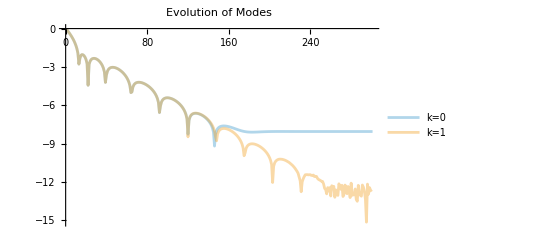

```mathematica
(*Parameters-Adjust these to match your simulation setup*)
g3=Obj[[;;,4,1,1,-1]];
(*4. Visualization*)
(*Plot the real part (oscillations) and the Magnitude (decay)*)
ListLinePlot[{(Re[g3])//Abs//Log[10,#]&,(Re[g3])-Re[g3[[-1]]]//Abs//Log[10,#]&},PlotRange->All,FrameLabel->{"Time Index","Amplitude"},PlotLabel->"Evolution of Modes",ImageSize->Full,PlotLegends->Placed[{"k=0","k=1","k=2","k=3","k=4","k=5"},{Right,Top}],PlotStyle->{Opacity[0.4]}]
```

```mathematica
0.1^4
```

0.0001

```mathematica
aaa=20;
bbb=40;
Timess=times;(*Table[(*dt*)dt (each i),{i,0,g3[[;;,1,1]]//Length}];*)
Lastg3=g3[[-1]];
Datag3=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*-Lastg3*)(*Lastg3[[1,1]]*))(*//Abs//Log*)}];
Datag3Log=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*Lastg3*))//Abs//Log}];
```

```mathematica
A0d5FitResgWr=NonlinearModelFit[Datag3,(*-wi (t-t0)+A1*)(*0.05 E^(-wi (t-t0))Cos[wr (t-t0)+ϕ]*)0.5 E^(-wi1(t-t01))Cos[wr1(t-t01)+ϕ1]/.wi1->Im[-ω1ot]/.wr1->Re[ω1ot](*/.t01->0.7407279439831308*)(*+A2 Exp[-wi2(t-t01)]Cos[wr2(t-t01)+ϕ2]*)(*+A2 +wi2(t-t01)*)(*+ 0.1 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w1i (t-t0))Cos[w1r (t-t0)+ϕ1]+*)(*A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0]*) (*A0oft[t]*)(*+a1g  E^(-w1gi (t))Cos[w1gr (t-t0)+ϕ1g]*)(*+a2g E^(-w2gi (t-t0))Cos[ w2gr (t-t0)+ϕ2g] *)
,{{A1},ϕ1,{wi1,4.955091289557959},{wr1,5.392238705862567},t01(*,{A2},ϕ2,{wi2},{wr2},t02*)},{t(*,Timess[[aaa]],Timess[[bbb]]*)},MaxIterations->5000,ConfidenceLevel->0.9999999999];
```

```mathematica
A0d5FitResgWr["BestFitParameters"]
```

{A1→1.,ϕ1→5.521,wi1→4.95509,wr1→5.39224,t01→0.0253242}

```mathematica
ω1ot
```

-5.169520975762229549404618858897224991945721855354884116-4.763570116920460863645146483709052189501385495221501904 ⅈ

```mathematica
A0d2FitResgWr["BestFitParameters"]
```

{A1→1.,ϕ1→6.30899,wi1→5.3,wr1→4.8,t01→0.0195779}

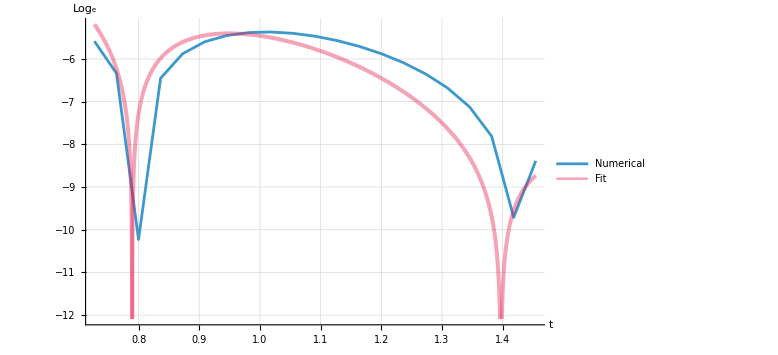

```mathematica
Show[ListPlot[Datag3Log,PlotStyle->PointSize[0.01],PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large,Joined->True],Plot[A0d5FitResgWr[t]//Abs//Log,{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.4],RGBColor[0.9,.1,0.3]}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

```mathematica
ClearAll[t];
aaa=90;
bbb=200;
Timess=times;(*Table[(*dt*)dt (each i),{i,0,g3[[;;,1,1]]//Length}];*)
Datag3=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*-Lastg3*)(*Lastg3[[1,1]]*))(*//Abs//Log*)}];
Datag3Log=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*Lastg3*))//Abs//Log}];
A0d5FitResgWr2=NonlinearModelFit[Datag3,(*-wi (t-t0)+A1*)A2 E^(-wi2 (t-t01))Cos[wr2 (t-t01)+ϕ2]/.wi2->Im[-ωfund]/.w2r->Re[ωfund](*+A3 E^(-wi2 (t-t01))Cos[-wr2 (t-t01)+ϕ3]*)/.A0d5FitResgWr["BestFitParameters"](*//Abs//Log*)(*+ 0.1 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w1i (t-t0))Cos[w1r (t-t0)+ϕ1]+*)(*A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0]*) (*A0oft[t]*)(*+a1g  E^(-w1gi (t))Cos[w1gr (t-t0)+ϕ1g]*)(*+a2g E^(-w2gi (t-t0))Cos[ w2gr (t-t0)+ϕ2g] *)
,{(*a1g,a2g,A2,A0,ϕ1g,ϕ2g,w1gi,w1gr,w2gi,w2gr,ϕ2,ϕ0,*)A2,ϕ2,t01,wi2,wr2,A3,ϕ3},{t(*,Timess[[aaa]],Timess[[bbb]]*)},MaxIterations->5000,ConfidenceLevel->0.9999999999];
```

```mathematica
A0d5FitResgWr2["BestFitParameters"]
```

{A2→0.100071,ϕ2→-8.77354,t01→1.,wi2→1.,wr2→3.10828,A3→1.,ϕ3→1.}

```mathematica
0.5^3
```

0.125

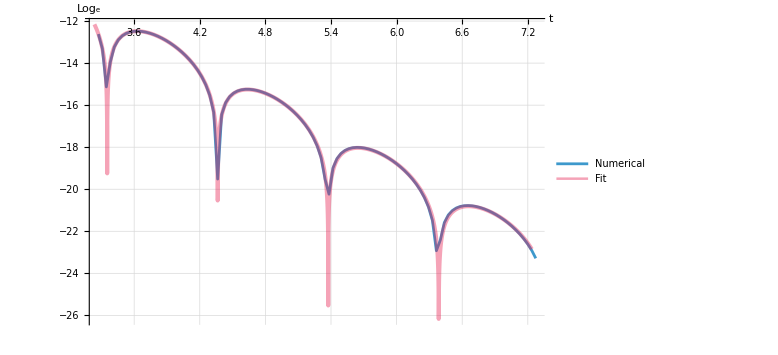

```mathematica
Timess=Table[(*dt*)dt (each i),{i,0,Obj//Length}];
Show[ListPlot[Datag3Log,PlotStyle->PointSize[0.01],PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large,Joined->True],Plot[A0d5FitResgWr2[t]//Abs//Log,{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.4],RGBColor[0.9,.1,0.3]}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

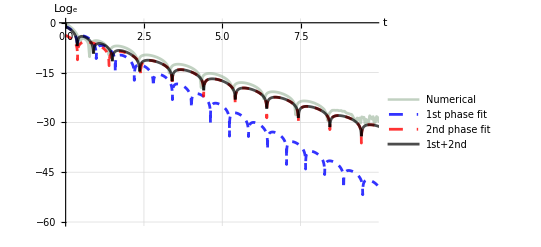

```mathematica
Show[ListPlot[Transpose[{Timess[[;;-2]],(g3[[;;]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*Lastg3*))//Abs//Log}],PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.6],RGBColor[0.6,0.7,0.6]},PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Full,Joined->True],Plot[A0d3FitResgWr[t]//Abs//Log,{t,Timess[[1]],Timess[[-1]]},PlotLegends->{"1st phase fit"},PlotStyle->{Blue,Opacity[0.8],Dashed},PlotLegends->Placed["Numerical", {Center}]],Plot[A0d3FitResgWr2[t]//Abs//Log,{t,Timess[[1]],Timess[[-1]]},PlotLegends->{"2nd phase fit"},PlotStyle->{Red,Opacity[0.8],Dashed}],Plot[A0d3FitResgWr[t]+A0d3FitResgWr2[t]//Abs//Log,{t,Timess[[1]],Timess[[-1]]},PlotLegends->{"1st+2nd"},PlotStyle->{Black,Opacity[0.7],Point}],PlotRange->{{0,9.8},{-60,0.1}},AxesLabel->{"t","Log_e"}]
```

```mathematica
Export["/home/giulio/Pictures/Jecco_QNM_gxy"<>FileName<>".pdf",%]
```

/home/giulio/Pictures/Jecco_QNM_gxyBB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d5.pdf

```mathematica
aaa=38;
bbb=343;
Timess=times;(*Table[(*dt*)dt (each i),{i,0,g3[[;;,1,1]]//Length}];*)
Datag3=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*-Lastg3*)(*Lastg3[[1,1]]*))(*//Abs//Log*)}];
Datag3Log=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb]]-g3[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*Lastg3*))//Abs//Log}];
```

Part::take: Cannot take positions 38 through 343 in {0.0363636,0.0727273,0.109091,0.145455,0.181818,0.218182,0.254545,0.290909,0.327273,0.363636,0.4,0.436364,0.472727,«25»,1.41818,1.45455,1.49091,1.52727,1.56364,1.6,1.63636,1.67273,1.70909,1.74545,1.78182,1.81818,«251»}.

Part::take: Cannot take positions 38 through 343 in {0.872356,0.675682,0.522455,0.401105,0.304309,0.227037,0.165298,0.116415,0.0781764,0.048942,0.0272946,0.01193,«28»,-0.000460828,-0.000641054,-0.000772699,-0.000860798,-0.000910889,-0.000928671,-0.00091975,-0.000889448,-0.00084269,-0.000783923,«251»}.

Part::take: Cannot take positions 38 through 343 in {0.0363636,0.0727273,0.109091,0.145455,0.181818,0.218182,0.254545,0.290909,0.327273,0.363636,0.4,0.436364,0.472727,«25»,1.41818,1.45455,1.49091,1.52727,1.56364,1.6,1.63636,1.67273,1.70909,1.74545,1.78182,1.81818,«251»}.

Part::take: Cannot take positions 38 through 343 in {0.872356,0.675682,0.522455,0.401105,0.304309,0.227037,0.165298,0.116415,0.0781764,0.048942,0.0272946,0.01193,«28»,-0.000460828,-0.000641054,-0.000772699,-0.000860798,-0.000910889,-0.000928671,-0.00091975,-0.000889448,-0.00084269,-0.000783923,«251»}.

```mathematica
A0d2FitResgWr3=NonlinearModelFit[Datag3,(*-wi (t-t0)+A1*)(*0.05 E^(-wi (t-t0))Cos[wr (t-t0)+ϕ]*)0.2 E^(-wi1(t-t01))Cos[wr1(t-t01)+ϕ1]+A2 Exp[-wi2(t-t01)]Cos[wr2(t-t01)+ϕ2](*/.A0d15FitResgWr["BestFitParameters"][[3;;4]]*)/.A0d2FitResgWr2["BestFitParameters"][[4;;5]](*+A2 +wi2(t-t01)*)(*+ 0.1 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w1i (t-t0))Cos[w1r (t-t0)+ϕ1]+*)(*A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0]*) (*A0oft[t]*)(*+a1g  E^(-w1gi (t))Cos[w1gr (t-t0)+ϕ1g]*)(*+a2g E^(-w2gi (t-t0))Cos[ w2gr (t-t0)+ϕ2g] *)
,{{A1,0.00015},ϕ1,{wi1,A0d15FitResgWr["BestFitParameters"][[3,2]]},{wr1,A0d15FitResgWr["BestFitParameters"][[4,2]]},{t01,0.001},{A2,0.0001},ϕ2,{wi2,A0d15FitResgWr2["BestFitParameters"][[4,2]]},{wr2,A0d15FitResgWr2["BestFitParameters"][[5,2]]},t02},{t(*,Timess[[aaa]],Timess[[bbb]]*)},MaxIterations->5000,ConfidenceLevel->0.9999999999];
```

NonlinearModelFit::nrlnum: The function value {0.000882879-1. Optimization`FindFit`y$280659,-1.71479×10^-6-1. Optimization`FindFit`y$280659} is not a list of real numbers with dimensions {2} at {A1,ϕ1,wi1,wr1,t01,A2,ϕ2,wi2,wr2,t02} = {0.00015,1.,5.3,4.8,0.001,0.0001,1.,1.,1.,1.}.

NonlinearModelFit::nrlnum: The function value {0.000882879-1. Optimization`FindFit`y$280674,-1.71479×10^-6-1. Optimization`FindFit`y$280674} is not a list of real numbers with dimensions {2} at {A1,ϕ1,wi1,wr1,t01,A2,ϕ2,wi2,wr2,t02} = {0.00015,1.,5.3,4.8,0.001,0.0001,1.,1.,1.,1.}.

```mathematica
A0d2FitResgWr3["BestFitParameters"]
```

NonlinearModelFit::nrlnum: The function value {0.000882879-1. Optimization`FindFit`y$280692,-1.71479×10^-6-1. Optimization`FindFit`y$280692} is not a list of real numbers with dimensions {2} at {A1,ϕ1,wi1,wr1,t01,A2,ϕ2,wi2,wr2,t02} = {0.00015,1.,5.3,4.8,0.001,0.0001,1.,1.,1.,1.}.

NonlinearModelFit[{{0.0363636,0.0727273,0.109091,0.145455,0.181818,0.218182,0.254545,0.290909,0.327273,0.363636,0.4,0.436364,0.472727,0.509091,0.545455,0.581818,0.618182,0.654545,0.690909,0.727273,0.763636,0.8,0.836364,0.872727,0.909091,0.945455,0.981818,1.01818,1.05455,1.09091,1.12727,1.16364,1.2,1.23636,1.27273,1.30909,1.34545,1.38182,1.41818,1.45455,1.49091,1.52727,1.56364,1.6,1.63636,1.67273,1.70909,1.74545,1.78182,1.81818,1.85455,1.89091,1.92727,1.96364,2.,2.03636,2.07273,2.10909,2.14545,2.18182,2.21818,2.25455,2.29091,2.32727,2.36364,2.4,2.43636,2.47273,2.50909,2.54545,2.58182,2.61818,2.65455,2.69091,2.72727,2.76364,2.8,2.83636,2.87273,2.90909,2.94545,2.98182,3.01818,3.05455,3.09091,3.12727,3.16364,3.2,3.23636,3.27273,3.30909,3.34545,3.38182,3.41818,3.45455,3.49091,3.52727,3.56364,3.6,3.63636,3.67273,3.70909,3.74545,3.78182,3.81818,3.85455,3.89091,3.92727,3.96364,4.,4.03636,4.07273,4.10909,4.14545,4.18182,4.21818,4.25455,4.29091,4.32727,4.36364,4.4,4.43636,4.47273,4.50909,4.54545,4.58182,4.61818,4.65455,4.69091,4.72727,4.76364,4.8,4.83636,4.87273,4.90909,4.94545,4.98182,5.01818,5.05455,5.09091,5.12727,5.16364,5.2,5.23636,5.27273,5.30909,5.34545,5.38182,5.41818,5.45455,5.49091,5.52727,5.56364,5.6,5.63636,5.67273,5.70909,5.74545,5.78182,5.81818,5.85455,5.89091,5.92727,5.96364,6.,6.03636,6.07273,6.10909,6.14545,6.18182,6.21818,6.25455,6.29091,6.32727,6.36364,6.4,6.43636,6.47273,6.50909,6.54545,6.58182,6.61818,6.65455,6.69091,6.72727,6.76364,6.8,6.83636,6.87273,6.90909,6.94545,6.98182,7.01818,7.05455,7.09091,7.12727,7.16364,7.2,7.23636,7.27273,7.30909,7.34545,7.38182,7.41818,7.45455,7.49091,7.52727,7.56364,7.6,7.63636,7.67273,7.70909,7.74545,7.78182,7.81818,7.85455,7.89091,7.92727,7.96364,8.,8.03636,8.07273,8.10909,8.14545,8.18182,8.21818,8.25455,8.29091,8.32727,8.36364,8.4,8.43636,8.47273,8.50909,8.54545,8.58182,8.61818,8.65455,8.69091,8.72727,8.76364,8.8,8.83636,8.87273,8.90909,8.94545,8.98182,9.01818,9.05455,9.09091,9.12727,9.16364,9.2,9.23636,9.27273,9.30909,9.34545,9.38182,9.41818,9.45455,9.49091,9.52727,9.56364,9.6,9.63636,9.67273,9.70909,9.74545,9.78182,9.81818,9.85455,9.89091,9.92727,9.96364,10.,10.0364,10.0727,10.1091,10.1455,10.1818,10.2182,10.2545,10.2909,10.3273,10.3636,10.4,10.4364,10.4727,10.5091,10.5455,10.5818,10.6182,10.6545,10.6909,10.7273,10.7636,10.8,10.8364,10.8727,10.9091,10.9455}⟦38;;343⟧,8.69046×10^-9+Re[{0.872356,0.675682,0.522455,0.401105,0.304309,0.227037,0.165298,0.116415,0.0781764,0.048942,0.0272946,0.01193,0.00163797,-0.00468458,-0.00800973,-0.0091649,-0.00883172,-0.00755512,-0.00575722,-0.00375413,-0.00177219,0.0000360662,0.00157744,0.00280504,0.00370669,0.00429506,0.00459951,0.00465932,0.00451849,0.00422186,0.00381236,0.00332904,0.00280596,0.00227174,0.00174941,0.00125659,0.000805941,0.000405766,0.0000606669,-0.000227868,-0.000460828,-0.000641054,-0.000772699,-0.000860798,-0.000910889,-0.000928671,-0.00091975,-0.000889448,-0.00084269,-0.000783923,-0.000717059,-0.000645454,-0.000571914,-0.00049872,-0.000427675,-0.000360151,-0.000297144,-0.000239322,-0.000187077,-0.000140573,-0.0000997901,-0.0000645653,-0.0000346279,-9.63106×10^-6,0.0000108222,0.0000271573,0.0000398109,0.0000492173,0.0000557981,0.0000599544,0.0000620619,0.0000624669,0.0000614849,0.0000593996,0.0000564631,0.0000528968,0.0000488928,0.0000446156,0.0000402043,0.0000357742,0.0000314196,0.0000272157,0.0000232204,0.000019477,0.0000160155,0.000012855,0.0000100048,7.46642×10^-6,5.23493×10^-6,3.30003×10^-6,1.64739×10^-6,2.59579×10^-7,-8.82989×10^-7,-1.80131×10^-6,-2.51711×10^-6,-3.05231×10^-6,-3.42852×10^-6,-3.6667×10^-6,-3.78683×10^-6,-3.80772×10^-6,-3.7468×10^-6,-3.62004×10^-6,-3.44191×10^-6,-3.2253×10^-6,-2.98159×10^-6,-2.72067×10^-6,-2.451×10^-6,-2.17971×10^-6,-1.91266×10^-6,-1.65459×10^-6,-1.40919×10^-6,-1.17925×10^-6,-9.66699×10^-7,-7.72792×10^-7,-5.98163×10^-7,-4.42934×10^-7,-3.06803×10^-7,-1.89133×10^-7,-8.90165×10^-8,-5.34937×10^-9,6.31137×10^-8,1.17708×10^-7,1.59812×10^-7,1.90814×10^-7,2.12084×10^-7,2.24942×10^-7,2.30644×10^-7,2.30367×10^-7,2.252×10^-7,2.16134×10^-7,2.04062×10^-7,1.89779×10^-7,1.73979×10^-7,1.57264×10^-7,1.40146×10^-7,1.2305×10^-7,1.06327×10^-7,9.02553×10^-8,7.50483×10^-8,6.08641×10^-8,4.78103×10^-8,3.59527×10^-8,2.53199×10^-8,1.5909×10^-8,7.6938×10^-9,6.27637×10^-10,-5.35189×10^-9,-1.03179×10^-8,-1.43512×10^-8,-1.75371×10^-8,-1.99631×10^-8,-2.17177×10^-8,-2.28852×10^-8,-2.35479×10^-8,-2.3784×10^-8,-2.36655×10^-8,-2.3259×10^-8,-2.26246×10^-8,-2.18175×10^-8,-2.08855×10^-8,-1.98707×10^-8,-1.88076×10^-8,-1.77287×10^-8,-1.66582×10^-8,-1.56172×10^-8,-1.46213×10^-8,-1.36833×10^-8,-1.28116×10^-8,-1.20132×10^-8,-1.12903×10^-8,-1.06448×10^-8,-1.00754×10^-8,-9.58089×10^-9,-9.15747×10^-9,-8.80095×10^-9,-8.50638×10^-9,-8.26918×10^-9,-8.08375×10^-9,-7.9443×10^-9,-7.84591×10^-9,-7.78223×10^-9,-7.74881×10^-9,-7.74119×10^-9,-7.7543×10^-9,-7.78474×10^-9,-7.82831×10^-9,-7.88181×10^-9,-7.94231×10^-9,-8.00714×10^-9,-8.07442×10^-9,-8.14254×10^-9,-8.20929×10^-9,-8.2737×10^-9,-8.33554×10^-9,-8.39363×10^-9,-8.44689×10^-9,-8.49594×10^-9,-8.53955×10^-9,-8.57878×10^-9,-8.61339×10^-9,-8.64277×10^-9,-8.66823×10^-9,-8.68958×10^-9,-8.707×10^-9,-8.72105×10^-9,-8.73136×10^-9,-8.73928×10^-9,-8.74491×10^-9,-8.74862×10^-9,-8.75008×10^-9,-8.74973×10^-9,-8.74868×10^-9,-8.74654×10^-9,-8.74382×10^-9,-8.7402×10^-9,-8.73656×10^-9,-8.73195×10^-9,-8.72784×10^-9,-8.72394×10^-9,-8.71939×10^-9,-8.71511×10^-9,-8.71151×10^-9,-8.70806×10^-9,-8.70462×10^-9,-8.70179×10^-9,-8.69901×10^-9,-8.69698×10^-9,-8.69504×10^-9,-8.69282×10^-9,-8.69168×10^-9,-8.69063×10^-9,-8.68946×10^-9,-8.68872×10^-9,-8.68785×10^-9,-8.6869×10^-9,-8.68684×10^-9,-8.68681×10^-9,-8.68695×10^-9,-8.68687×10^-9,-8.68687×10^-9,-8.68729×10^-9,-8.68724×10^-9,-8.6871×10^-9,-8.68788×10^-9,-8.68775×10^-9,-8.68783×10^-9,-8.6886×10^-9,-8.68892×10^-9,-8.68907×10^-9,-8.6892×10^-9,-8.68937×10^-9,-8.6894×10^-9,-8.68979×10^-9,-8.69016×10^-9,-8.69021×10^-9,-8.69035×10^-9,-8.69011×10^-9,-8.69065×10^-9,-8.69081×10^-9,-8.69054×10^-9,-8.69096×10^-9,-8.69088×10^-9,-8.6909×10^-9,-8.6904×10^-9,-8.69069×10^-9,-8.69035×10^-9,-8.69055×10^-9,-8.69116×10^-9,-8.69092×10^-9,-8.69072×10^-9,-8.691×10^-9,-8.69053×10^-9,-8.69057×10^-9,-8.69102×10^-9,-8.69086×10^-9,-8.69058×10^-9,-8.69089×10^-9,-8.69072×10^-9,-8.69052×10^-9,-8.69125×10^-9,-8.69037×10^-9,-8.69037×10^-9,-8.69037×10^-9,-8.69019×10^-9,-8.69042×10^-9,-8.69043×10^-9,-8.69099×10^-9,-8.69056×10^-9,-8.69055×10^-9,-8.69039×10^-9,-8.69102×10^-9,-8.69084×10^-9,-8.69064×10^-9,-8.69051×10^-9,-8.69046×10^-9,-8.69112×10^-9,-8.69057×10^-9,-8.69081×10^-9,-8.69069×10^-9,-8.69063×10^-9,-8.69046×10^-9}⟦38;;343⟧]},0.2 ⅇ^(-((t-t01) wi1)) Cos[(t-t01) wr1+ϕ1]+A2 ⅇ^(-2.7488 (t-t01)) Cos[3.11986 (t-t01)+ϕ2],{{A1,0.00015},ϕ1,{wi1,5.3},{wr1,4.8},{t01,0.001},{A2,0.0001},ϕ2,{wi2,1.},{wr2,1.},t02},{t},MaxIterations→5000,ConfidenceLevel→1.][BestFitParameters]

```mathematica
A0d2FitResgWr["BestFitParameters"]
A0d2FitResgWr2["BestFitParameters"]
```

{A1→1.,ϕ1→6.30899,wi1→5.3,wr1→4.8,t01→0.0195779}

{A2→0.00646494,ϕ2→-8.91304,t02→1.,wi2→2.7488,wr2→3.11986}

```mathematica
Show[ListPlot[Datag3Log,PlotStyle->PointSize[0.01],PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large,Joined->True],Plot[A0d2FitResgWr3[t]//Abs//Log,{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.4],RGBColor[0.9,.1,0.3]}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

Part::take: Cannot take positions 38 through 343 in {0.0363636,0.0727273,0.109091,0.145455,0.181818,0.218182,0.254545,0.290909,0.327273,0.363636,0.4,0.436364,0.472727,«25»,1.41818,1.45455,1.49091,1.52727,1.56364,1.6,1.63636,1.67273,1.70909,1.74545,1.78182,1.81818,«251»}.

Part::partw: Part 343 of {0.0363636,0.0727273,0.109091,0.145455,0.181818,0.218182,0.254545,0.290909,0.327273,0.363636,0.4,0.436364,0.472727,«25»,1.41818,1.45455,1.49091,1.52727,1.56364,1.6,1.63636,1.67273,1.70909,1.74545,1.78182,1.81818,«251»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {0.0363636,0.0727273,0.109091,0.145455,0.181818,0.218182,0.254545,0.290909,0.327273,0.363636,0.4,0.436364,0.472727,«25»,1.41818,1.45455,1.49091,1.52727,1.56364,1.6,1.63636,1.67273,1.70909,1.74545,1.78182,1.81818,«251»}«1»«3»⟧ in {t,«18»,{0.0363636,0.0727273,0.109091,0.145455,0.181818,0.218182,0.254545,0.290909,0.327273,0.363636,0.4,0.436364,0.472727,«26»,1.45455,1.49091,1.52727,1.56364,1.6,1.63636,1.67273,1.70909,1.74545,1.78182,1.81818,«251»}⟦343⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,Plot[Log[Abs[A0d2FitResgWr3[t]]],{t,Timess⟦aaa⟧,Timess⟦bbb⟧},PlotLegends→{Fit},PlotStyle→{PointSize[0.006],Thickness[0.005],Opacity[0.4],color}],PlotRange→All,AxesLabel→{t,Log_e}].

Show[-Graphics-,Plot[Log[Abs[A0d2FitResgWr3[t]]],{t,Timess⟦aaa⟧,Timess⟦bbb⟧},PlotLegends→{Fit},PlotStyle→{PointSize[0.006],Thickness[0.005],Opacity[0.4],RGBColor[0.9, 0.1, 0.3]}],PlotRange→All,AxesLabel→{t,Log_e}]

### Amplitudes scaling analysis

```mathematica
A0d3FitResgWr2["BestFitParameters"][[1,2]]
```

-0.0227347

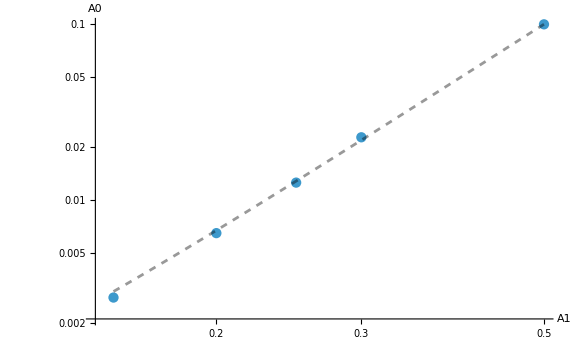

```mathematica
Amplitudes={{0.15,A0d15FitResgWr2["BestFitParameters"][[1,2]]},{0.2,A0d2FitResgWr2["BestFitParameters"][[1,2]]},{0.25,A0d25FitResgWr2["BestFitParameters"][[1,2]]},{0.3,A0d3FitResgWr2["BestFitParameters"][[1,2]]},{0.5,A0d5FitResgWr2["BestFitParameters"][[1,2]]}}//Abs;
AmplFit=NonlinearModelFit[Amplitudes,a x^3+b,{a,b},x];
Show[ListLogLogPlot[Amplitudes//Abs,PlotRange->All(*,Joined->True*),ImageSize->Large,AxesLabel->{"A1","A0"},PlotLegends->Placed[{"Amp"},{Right,Center}]],LogLogPlot[AmplFit[x],{x,0.15,0.5},PlotStyle->{Black,Opacity[0.4],Dashed},PlotLegends->Placed[{"fit"},{Right,Center}]]]
```

```mathematica
Export["/home/giulio/Pictures/Jecco5DQNMCubicRelation.pdf",%]
```

/home/giulio/Pictures/Jecco5DQNMCubicRelation.pdf